```mathematica
With[{
pos={"SPY","IVV","VOO","SSO","SH","UPRO","SPXL","SDS","SPXU","SPXS","PPLC","SPDN","SPUU"},
neg={"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX"}
},
With[{
spx=FinancialData["^SPX","Close",{{2018},{2020}}],
vix=FinancialData["VIX","Close",{{2018},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@f,Apply[Correlation,Last@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
]
```

```mathematica
Map[FinancialData[#,"Name"]&,{"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX","EXIV","XVZ","EVIX"}]
```

$Aborted

```mathematica
ParallelMap[FinancialData[#,"Name"]&,{"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX","EXIV","XVZ","EVIX"}]
```

Initializing FinancialData indices ....

Initializing FinancialData indices ....

Initializing FinancialData indices ....

«5 more identical outputs»

FinancialData::notent: EXIV is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: XVZ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: EVIX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{Barclays Bank iPath Exch Traded Nts 2009-30.1.19 iPath S&P 500 VIX Short Term Futures Ser A,CS Nassau VelocityShares Daily 2x VIX Short Term Exchange Traded Notes 2015-4.12.30 Linked to S&P 50,ProShares Trust - ProShares Ultra VIX Short-Term Futures ETF,ProShares Trust - ProShares VIX Short-Term Futures ETF,ProShares Trust - ProShares Short VIX Short-Term Futures ETF,VELOCITYSHARES DAILY INVERSE,ProShares Trust - ProShares VIX Mid-Term Futures ETF,iPath S&P 500 VIX Mid-Term FuturesTM ETN,CS Nassau Underlying Tracker 2017-04.12.30 (Exp.30.11.30) on S&P 500 VIX STF ER,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
ParallelMap[FinancialData[StringJoin["^",#],"Name"]&,{"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX","EXIV","XVZ","EVIX"}]
```

FinancialData::notent: ^EXIV is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^VIXM is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^VXX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^VXZ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^VIXY is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^XVZ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^TVIX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^VIIX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: ^SVXY is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

FinancialData::notent: ^EVIX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

FinancialData::notent: ^UVXY is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

FinancialData::notent: ^ZIV is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
Grid@
Map[
{#,FinancialData[#,"Name"]}&,
{"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX","EXIV","XVZ","EVIX"}]
```

FinancialData::notent: EXIV is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: XVZ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: EVIX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

VXX | Barclays Bank iPath Exch Traded Nts 2009-30.1.19 iPath S&P 500 VIX Short Term Futures Ser A
TVIX | CS Nassau VelocityShares Daily 2x VIX Short Term Exchange Traded Notes 2015-4.12.30 Linked to S&P 50
UVXY | ProShares Trust - ProShares Ultra VIX Short-Term Futures ETF
VIXY | ProShares Trust - ProShares VIX Short-Term Futures ETF
SVXY | ProShares Trust - ProShares Short VIX Short-Term Futures ETF
ZIV | VELOCITYSHARES DAILY INVERSE
VIXM | ProShares Trust - ProShares VIX Mid-Term Futures ETF
VXZ | iPath S&P 500 VIX Mid-Term FuturesTM ETN
VIIX | CS Nassau Underlying Tracker 2017-04.12.30 (Exp.30.11.30) on S&P 500 VIX STF ER
EXIV | Missing[NotAvailable]
XVZ | Missing[NotAvailable]
EVIX | Missing[NotAvailable]

```mathematica
Grid@
Map[
{#,FinancialData[#,"Name"]}&,
{"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX"}]
```

VXX | Barclays Bank iPath Exch Traded Nts 2009-30.1.19 iPath S&P 500 VIX Short Term Futures Ser A
TVIX | CS Nassau VelocityShares Daily 2x VIX Short Term Exchange Traded Notes 2015-4.12.30 Linked to S&P 50
UVXY | ProShares Trust - ProShares Ultra VIX Short-Term Futures ETF
VIXY | ProShares Trust - ProShares VIX Short-Term Futures ETF
SVXY | ProShares Trust - ProShares Short VIX Short-Term Futures ETF
ZIV | VELOCITYSHARES DAILY INVERSE
VIXM | ProShares Trust - ProShares VIX Mid-Term Futures ETF
VXZ | iPath S&P 500 VIX Mid-Term FuturesTM ETN
VIIX | CS Nassau Underlying Tracker 2017-04.12.30 (Exp.30.11.30) on S&P 500 VIX STF ER

```mathematica
Grid@
Map[
{#,FinancialData[String[#],"Name"]}&,
{SPY,
IVV,
VOO,
SSO,
SH,
UPRO,
SPXL,
SDS,
SPXU,
SPXS,
PPLC,
SPDN,
SPUU}
]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[String[SPY],{AbuDhabiSecuritiesExchange,AktieTorget,AmmanStockExchange,AmsterdamStockExchange,AthensExchange,AustralianSecuritiesExchange,BahrainStockExchange,BanjaLukaStockExchange,BatsGlobalMarkets,BelgradeStockExchange,BerlinStockExchange,BermudaStockExchange,BombayStockExchange,BourseRegionaleDesValeursMobilieres,BratislavaStockExchange,BrusselsStockExchange,BudapestStockExchange,«18»,GuayaquilStockExchange,HamburgStockExchange,HanoverStockExchange,HoChiMinhCityStockExchange,HongKongStockExchange,ICEFuturesUS,IndonesiaStockExchange,IraqStockExchange,IrishStockExchange,IstanbulStockExchange,ItalianExchange,JamaicaStockExchange,JASDAQ,JohannesburgStockExchange,KansasCityBoardOfTrade,«80»},IgnoreCase→True].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[String[SPY],{AmmanStockExchange,AmsterdamStockExchange,AthensExchange,BahrainStockExchange,BanjaLukaStockExchange,BatsGlobalMarkets,BelgradeStockExchange,BerlinStockExchange,BombayStockExchange,BotswanaStockExchange,BourseRegionaleDesValeursMobilieres,BratislavaStockExchange,BrusselsStockExchange,BucharestStockExchange,BudapestStockExchange,BulgarianStockExchange,BursaMalaysia,«18»,HanoverStockExchange,HoChiMinhCityStockExchange,HongKongStockExchange,IndonesiaStockExchange,IrishStockExchange,IstanbulStockExchange,ItalianExchange,JamaicaStockExchange,KarachiStockExchange,KazakhstanStockExchange,KoreanStockExchange,KuwaitExchange,LimaStockExchange,LisbonStockExchange,LjubljanaStockMarket,«56»},IgnoreCase→True].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[String[SPY],{AdvertisingAgencies,AerospaceAndDefense,AgriculturalInputs,Airlines,AirportsAndAirServices,Aluminum,ApparelManufacturing,ApparelStores,AssetManagement,AutoAndTruckDealerships,AutoManufacturers,AutoParts,Banks-Global,Banks-Regional-Africa,Banks-Regional-Asia,Banks-Regional-Australia,Banks-Regional-Canada,Banks-Regional-Europe,«15»,ComputerDistribution,ComputerSystems,Confectioners,Conglomerates,ConsumerElectronics,ContractManufacturers,Copper,CreditServices,DataStorage,DepartmentStores,DiagnosticsAndResearch,DiscountStores,DiversifiedIndustrials,DrugManufacturers-Major,DrugManufacturers-SpecialtyAndGeneric,EducationAndTrainingServices,ElectronicComponents,«98»},IgnoreCase→True].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

StringFreeQ::strse: String or list of strings expected at position 1 in StringFreeQ[String[SPY],*|@].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[String[SPY],StringPattern`Dump`CapGr[1,NASDAQCM:|NASDAQGM:|NASDAQGS:]:>NASDAQ:,IgnoreCase→True].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

StringExpression::invld: Element StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True] is not a valid string or pattern element in AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True].

Pick::incomp: Expressions {^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»} and StringMatchQ[{^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»},AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True],IgnoreCase→True] have incompatible shapes.

Pattern::argr: Pattern called with 1 argument; 2 arguments are expected.

StringExpression::invld: Element StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True] is not a valid string or pattern element in AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True].

Pick::incomp: Expressions {^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»} and StringMatchQ[{^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»},AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True],IgnoreCase→True] have incompatible shapes.

Pattern::argr: Pattern called with 1 argument; 2 arguments are expected.

StringExpression::invld: Element StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True] is not a valid string or pattern element in AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True].

General::stop: Further output of StringExpression::invld will be suppressed during this calculation.

Pick::incomp: Expressions {^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»} and StringMatchQ[{^0000,^07Q9,^0DJ0,^0DJ1,^0DJ2,^0DJ3,^0DJ4,^0DJ5,^0DJ6,^0DJ7,^0DJ8,^0DJ9,^0DJA,^0DJB,^0DJC,^0DJD,^0DJE,^0DJF,^0DJS,^0DJT,^0DJU,^0DJV,^0DJW,^0DJX,^0DJY,^0DJZ,^0EX0,^0EX1,^0EX2,^0EX3,^0EX4,^0EX5,^0EX6,^0EX7,^0EX8,^0EX9,^0EXA,^0EXB,^0EXC,^0EXD,^0EXE,^0EXF,^0EXG,^0EXH,^0EXJ,^0EXK,^0EXL,^0EXM,^0EXN,^0EXP,«255788»},AMEX:|NYSE:|NASDAQ:|~~StringReplace[String[SPY],DataPaclets`FinancialDataDump`sub:NASDAQCM:|NASDAQGM:|NASDAQGS::>NASDAQ:,IgnoreCase→True],IgnoreCase→True] have incompatible shapes.

General::stop: Further output of Pick::incomp will be suppressed during this calculation.

Pattern::argr: Pattern called with 1 argument; 2 arguments are expected.

General::stop: Further output of Pattern::argr will be suppressed during this calculation.

Replace::reps: {If[«1»],«2»,If[StringMatchQ[String[SPY],{ADS,AMEX,AS,AX,BA,BATS,BD,BE,BG,BH,BK,BO,BR,CBOT,CL,CME,CNSX,CO,COMEX,CR,CY,DE,DFM,DH,DIFX,DSMD,DU,EE,F,FI,FU,GH,GR,GT,HA,HK,HM,HU,ICEUS,IDX,IE,IQS,IR,IS,ISX,JO,JQ,KA,KCBT,KE,«92»}~~:~~__]||StringMatchQ[String[SPY],^~~__]||StringMatchQ[String[SPY],Repeated[{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z},{5}]],«1»,If[Length[FinancialData[String[SPY],Lookup]]===1,Entity[Financial,Replace[«1»,«1»]],With[{DataPaclets`FinancialDataDump`interpretedEntity$=Quiet[Interpreter[«1»][«1»]]},Switch[DataPaclets`FinancialDataDump`interpretedEntity$,«11»,DataPaclets`FinancialDataDump`interpretedEntity$]]]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringFreeQ::strse: String or list of strings expected at position 1 in StringFreeQ[String[IVV],*|@].

Replace::reps: {If[«1»],«2»,If[StringMatchQ[String[IVV],{ADS,AMEX,AS,AX,BA,BATS,BD,BE,BG,BH,BK,BO,BR,CBOT,CL,CME,CNSX,CO,COMEX,CR,CY,DE,DFM,DH,DIFX,DSMD,DU,EE,F,FI,FU,GH,GR,GT,HA,HK,HM,HU,ICEUS,IDX,IE,IQS,IR,IS,ISX,JO,JQ,KA,KCBT,KE,«92»}~~:~~__]||StringMatchQ[String[IVV],^~~__]||StringMatchQ[String[IVV],Repeated[{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z},{5}]],«1»,If[Length[FinancialData[String[IVV],Lookup]]===1,Entity[Financial,Replace[«1»,«1»]],With[{DataPaclets`FinancialDataDump`interpretedEntity$=Quiet[Interpreter[«1»][«1»]]},Switch[DataPaclets`FinancialDataDump`interpretedEntity$,«11»,DataPaclets`FinancialDataDump`interpretedEntity$]]]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringFreeQ::strse: String or list of strings expected at position 1 in StringFreeQ[String[VOO],*|@].

General::stop: Further output of StringFreeQ::strse will be suppressed during this calculation.

$Aborted[]

General::stop: Further output of Replace::reps will be suppressed during this calculation.

$Aborted

```mathematica
Grid@
Map[
{#,FinancialData[#,"Name"]}&,
{"SPY","IVV","VOO","SSO","SH","UPRO","SPXL","SDS","SPXU","SPXS","PPLC","SPDN","SPUU"}
]
```

SPY | SSgA Active Trust - SSGA SPDR S&P 500
IVV | BlackRock Institutional Trust Company N.A. - BTC iShares Core S&P 500 ETF
VOO | Vanguard Group, Inc. - Vanguard S&P 500 ETF
SSO | ProShares Trust - ProShares Ultra S&P500
SH | ProShares Trust - ProShares Short S&P500
UPRO | ProShares Trust - ProShares UltraPro S&P 500 ETF
SPXL | Direxion Shares ETF Trust - Direxion Daily S&P 500 Bull 3X Shares
SDS | ProShares Trust - ProShares UltraShort S&P500
SPXU | ProShares Trust - ProShares UltraPro Short S&P 500 ETF
SPXS | Direxion Shares ETF Trust - Direxion Daily S&P 500 Bear 3X Shares
PPLC | Direxion Shares ETF Trust - PortfolioPlus S&P 500 ETF
SPDN | Direxion Shares ETF Trust - Direxion Daily S&P 500 Bear 1X Shares
SPUU | Direxion Shares ETF Trust - Direxion Daily S&P 500 Bull 2X Shares

```mathematica
With[{
pos={"SPY","IVV","VOO","SSO","SH","UPRO","SPXL","SDS","SPXU","SPXS","PPLC","SPDN","SPUU"},
neg={"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX"}
},
Join[pos,neg]
]
```

{SPY,IVV,VOO,SSO,SH,UPRO,SPXL,SDS,SPXU,SPXS,PPLC,SPDN,SPUU,VXX,TVIX,UVXY,VIXY,SVXY,ZIV,VIXM,VXZ,VIIX}

```mathematica
With[{
pos={"SPY","IVV","VOO","SSO","SH","UPRO","SPXL","SDS","SPXU","SPXS","PPLC","SPDN","SPUU"},
neg={"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX"}
},
{
ParallelTable[
FinancialData[i,"Close",All],
{i,pos}],
ParallelTable[
FinancialData[i,"Close",All],
{i,neg}]
}
]
```

{{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
ParallelTable[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
Grid@
ReverseSortBy[
{spx,vix,(Total@corr)/(Length@corr)}
,Last]
]
]
]
]
]
]
]
]
,{iii,Outer[{#1,#2}&,pos,neg]}]
]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[QuantityArray,{26612.5,25407.5,23437.5,22360.,21717.5,21035.,21020.,20605.,20877.5,20962.5,20877.5,21300.,19842.5,20037.5,20563.8,20635.,19375.,18962.5,18122.5,17000.,17410.,17407.5,17070.,«2217»,36.41,34.43,32.93,32.19,31.91,32.25,31.46,31.75,31.99,31.7901,31.59,32.25,33.54,32.07,30.75,32.37,31.95,31.79,31.14,30.02,29.91,29.1,28.93},«1»,{«1»}]]},«6»},True,12.]}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6760},StructuredArray`StructuredData[«4»]]},{{{«6760»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2352},StructuredArray`StructuredData[«4»]]},{{{«2352»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{3405},StructuredArray`StructuredData[«4»]]},{{{«3405»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[«4»]]},{{{«2816»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[V…s]].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::iterb: Iterator {f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{5159},StructuredArray`StructuredData[QuantityArray,{285.,287.5,286.,274.5,290.,287.,284.,280.,288.5,287.,292.,292.,289.,288.,287.5,286.5,282.,283.5,281.5,262.5,271.5,253.5,263.5,261.5,259.5,«5110»,26.53,26.38,25.94,25.89,25.53,25.53,25.53,25.33,25.09,25.03,24.95,24.7,24.7,24.98,24.86,24.41,24.74,24.61,24.74,24.49,24.16,24.3,23.96,24.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation «1» is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{5159},StructuredArray`StructuredData[QuantityArray,{285.,287.5,286.,274.5,290.,287.,284.,280.,288.5,287.,292.,292.,289.,288.,287.5,286.5,282.,283.5,281.5,262.5,271.5,253.5,263.5,261.5,259.5,«5110»,26.53,26.38,25.94,25.89,25.53,25.53,25.53,25.33,25.09,25.03,24.95,24.7,24.7,24.98,24.86,24.41,24.74,24.61,24.74,24.49,24.16,24.3,23.96,24.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[QuantityArray,{29.97,30.27,30.3525,30.42,30.39,30.525,30.8925,31.1925,31.2668,31.2375,31.0575,30.6075,30.7875,30.8475,31.005,31.4775,31.515,«1345»,66.6563,66.2107,66.1943,66.7752,66.86,66.0688,66.3893,67.5994,66.767,67.15,66.77,67.4609,68.3463,67.96,68.885,68.6112},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[«4»]]},{{{«971»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[«4»]]},{{{«907»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[«4»]]},{{{«1378»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[«4»]]},{{{«2658»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[QuantityArray,{29.97,30.27,30.3525,30.42,30.39,30.525,30.8925,31.1925,31.2668,31.2375,31.0575,30.6075,30.7875,30.8475,31.005,31.4775,31.515,«1345»,66.6563,66.2107,66.1943,66.7752,66.86,66.0688,66.3893,67.5994,66.767,67.15,66.77,67.4609,68.3463,67.96,68.885,68.6112},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation «1» is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::iterb: Iterator {f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::iterb: Iterator {f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

{Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}],Grid[{1/2 Total[Table[Correlation@@Last[f],{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}]],{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}]}

```mathematica
Outer[{a,b,c},{1,2,3}]
```

{{a,b,c}[1],{a,b,c}[2],{a,b,c}[3]}

```mathematica
Outer[Identity,{a,b},{x,y,z}]
```

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

General::stop: Further output of Identity::argx will be suppressed during this calculation.

{{Identity[a,x],Identity[a,y],Identity[a,z]},{Identity[b,x],Identity[b,y],Identity[b,z]}}

```mathematica
Outer[{#1,#2}&,{a,b},{x,y,z}]
```

{{{a,x},{a,y},{a,z}},{{b,x},{b,y},{b,z}}}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Table[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
Grid@
ReverseSortBy[
{spx,vix}
,Last]
]
]
]
]
]
]
]
]
,{iii,Outer[{#1,#2}&,pos,neg]}]
]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[QuantityArray,{26612.5,25407.5,23437.5,22360.,21717.5,21035.,21020.,20605.,20877.5,20962.5,20877.5,21300.,19842.5,20037.5,20563.8,20635.,19375.,18962.5,18122.5,17000.,17410.,17407.5,17070.,«2217»,36.41,34.43,32.93,32.19,31.91,32.25,31.46,31.75,31.99,31.7901,31.59,32.25,33.54,32.07,30.75,32.37,31.95,31.79,31.14,30.02,29.91,29.1,28.93},«1»,{«1»}]]},«6»},True,12.]}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6760},StructuredArray`StructuredData[«4»]]},{{{«6760»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[Values]].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::iterb: Iterator {f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Transpose::tperm: Permutation {«1»} is longer than the dimensions {2} of the expression.

General::stop: Further output of Transpose::tperm will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

{TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…],TimeSeries[…] | TimeSeries[…]
TimeSeries[…] | TimeSeries[…]}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Table[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
Grid@
ReverseSortBy[
corr
,Last]
]
]
]
]
]
]
]
]
,{iii,Outer[{#1,#2}&,pos,neg]}]
]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[QuantityArray,{26612.5,25407.5,23437.5,22360.,21717.5,21035.,21020.,20605.,20877.5,20962.5,20877.5,21300.,19842.5,20037.5,20563.8,20635.,19375.,18962.5,18122.5,17000.,17410.,17407.5,17070.,«2217»,36.41,34.43,32.93,32.19,31.91,32.25,31.46,31.75,31.99,31.7901,31.59,32.25,33.54,32.07,30.75,32.37,31.95,31.79,31.14,30.02,29.91,29.1,28.93},«1»,{«1»}]]},«6»},True,12.]}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6760},StructuredArray`StructuredData[«4»]]},{{{«6760»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[Values]].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::iterb: Iterator {f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[f].

Correlation::shlen: The argument f should have at least two elements.

Table::nliter: Non-list iterator Correlation@@Last[f] at position 2 does not evaluate to a real numeric value.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Correlation::shlen: The argument f should have at least two elements.

General::stop: Further output of Correlation::shlen will be suppressed during this calculation.

Table::nliter: Non-list iterator Correlation@@Last[f] at position 2 does not evaluate to a real numeric value.

Transpose::tperm: Permutation {«1»} is longer than the dimensions {2} of the expression.

General::stop: Further output of Transpose::tperm will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

Table::nliter: Non-list iterator Correlation@@Last[f] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

{Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]],Grid[Table[{f,Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]},Correlation@@Last[f]]]}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
ParallelTable[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
secondtable
]
]
]
]
]
]
]
,{iii,Outer[{#1,#2}&,pos,neg]}]
]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[QuantityArray,{26612.5,25407.5,23437.5,22360.,21717.5,21035.,21020.,20605.,20877.5,20962.5,20877.5,21300.,19842.5,20037.5,20563.8,20635.,19375.,18962.5,18122.5,17000.,17410.,17407.5,17070.,«2217»,36.41,34.43,32.93,32.19,31.91,32.25,31.46,31.75,31.99,31.7901,31.59,32.25,33.54,32.07,30.75,32.37,31.95,31.79,31.14,30.02,29.91,29.1,28.93},«1»,{«1»}]]},«6»},True,12.]}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[QuantityArray,{26612.5,25407.5,23437.5,22360.,21717.5,21035.,21020.,20605.,20877.5,20962.5,20877.5,21300.,19842.5,20037.5,20563.8,20635.,19375.,18962.5,18122.5,17000.,17410.,17407.5,17070.,«2217»,36.41,34.43,32.93,32.19,31.91,32.25,31.46,31.75,31.99,31.7901,31.59,32.25,33.54,32.07,30.75,32.37,31.95,31.79,31.14,30.02,29.91,29.1,28.93},«1»,{«1»}]]},«6»},True,12.]}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{3405},StructuredArray`StructuredData[«4»]]},{{{«3405»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[«4»]]},{{{«2816»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{6760},StructuredArray`StructuredData[«4»]]},{{{«6760»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2352},StructuredArray`StructuredData[«4»]]},{{{«2352»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[V…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[Values]].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2816},StructuredArray`StructuredData[QuantityArray,{4.25,3.6,3.85416,3.70416,3.45883,3.07416,3.51833,3.0675,2.85083,2.87666,2.41333,1.99666,2.2225,2.5975,2.7425,3.02833,2.30833,«2782»,64.94,65.89,65.76,65.78,66.78,66.74,65.57,66.08,67.91,66.28,67.05,66.54,67.56,68.93,68.28,69.76,69.38},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«6»[«1»]} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[«1»]},{{{2937254400,2937513600,2937600000,2937686400,2937772800,2937859200,2938118400,2938204800,2938291200,2938377600,2938464000,2938809600,2938896000,2938982400,2939068800,2939328000,2939414400,2939500800,2939587200,2939673600,2939932800,2940019200,2940105600,2940192000,2940278400,2940537600,2940624000,2940710400,2940796800,2940883200,2941142400,2941228800,2941315200,2941401600,2941488000,2941747200,2941833600,2941920000,2942006400,2942092800,2942352000,2942438400,2942524800,2942611200,2942697600,2942956800,2943043200,2943129600,2943216000,2943561600,«6710»}}},1,{…,1},{Discrete,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{5159},StructuredArray`StructuredData[QuantityArray,{285.,287.5,286.,274.5,290.,287.,284.,280.,288.5,287.,292.,292.,289.,288.,287.5,286.5,282.,283.5,281.5,262.5,271.5,253.5,263.5,261.5,259.5,«5110»,26.53,26.38,25.94,25.89,25.53,25.53,25.53,25.33,25.09,25.03,24.95,24.7,24.7,24.98,24.86,24.41,24.74,24.61,24.74,24.49,24.16,24.3,23.96,24.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation «1» is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{5159},StructuredArray`StructuredData[QuantityArray,{285.,287.5,286.,274.5,290.,287.,284.,280.,288.5,287.,292.,292.,289.,288.,287.5,286.5,282.,283.5,281.5,262.5,271.5,253.5,263.5,261.5,259.5,«5110»,26.53,26.38,25.94,25.89,25.53,25.53,25.53,25.33,25.09,25.03,24.95,24.7,24.7,24.98,24.86,24.41,24.74,24.61,24.74,24.49,24.16,24.3,23.96,24.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[QuantityArray,{29.97,30.27,30.3525,30.42,30.39,30.525,30.8925,31.1925,31.2668,31.2375,31.0575,30.6075,30.7875,30.8475,31.005,31.4775,31.515,«1345»,66.6563,66.2107,66.1943,66.7752,66.86,66.0688,66.3893,67.5994,66.767,67.15,66.77,67.4609,68.3463,67.96,68.885,68.6112},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[«4»]]},{{{«907»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[«4»]]},{{{«1378»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[«4»]]},{{{«2658»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[«4»]]},{{{«971»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},StructuredArray`StructuredData[«4»]]},{{{«2263»}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},True,12.]}[Values]].

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} cannot be transposed.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{1378},StructuredArray`StructuredData[QuantityArray,{29.97,30.27,30.3525,30.42,30.39,30.525,30.8925,31.1925,31.2668,31.2375,31.0575,30.6075,30.7875,30.8475,31.005,31.4775,31.515,«1345»,66.6563,66.2107,66.1943,66.7752,66.86,66.0688,66.3893,67.5994,66.767,67.15,66.77,67.4609,68.3463,67.96,68.885,68.6112},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[…s]].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[Values]].

General::stop: Further output of Ratios::listrp will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} cannot be transposed.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{907},StructuredArray`StructuredData[QuantityArray,{39.86,39.86,40.3,40.5602,40.7,40.74,40.868,40.76,40.52,40.28,40.44,39.9,41.28,42.18,41.3652,40.6564,40.1598,«874»,24.5364,24.45,24.4648,24.34,24.34,24.49,24.431,24.21,24.39,24.3,24.36,24.2486,24.07,24.16,24.0001,24.0392},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation «1» is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2658},StructuredArray`StructuredData[QuantityArray,{5863.2,5906.4,5730.4,5870.4,5808.8,6272.,6272.,6257.6,6635.2,6634.4,6620.,6664.,6168.8,6060.8,5529.6,5384.,5381.6,5216.,5136.8,5132.,«2619»,20.84,20.82,20.57,20.25,20.21,20.13,19.83,19.84,20.19,20.02,19.49,19.92,19.7,19.89,19.57,19.19,19.35,18.95,19.05},«1»,{«1»}]]},«5»,{«1»}},True,12.],«1»}[],«1»} is longer than the dimensions {2} of the expression.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{971},StructuredArray`StructuredData[QuantityArray,{25.26,25.87,25.6655,25.46,25.25,25.55,25.49,25.99,25.42,25.47,25.07,25.73,25.93,25.9,25.71,25.8699,26.07,«937»,44.5,44.8,44.4329,44.4197,44.698,44.7324,44.41,44.5451,45.09,44.71,44.8584,44.71,45.0369,45.44,45.27,45.6589,45.6},«1»,{«1»}]]},«5»,{«1»}},True,12.],«12»[«1»]}[],«1»} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{2263},«1»]},{{{3500064000,3500150400,3500236800,3500323200,3500668800,3500755200,3500841600,3500928000,3501187200,3501273600,3501360000,3501446400,3501878400,3502051200,3502656000,3502742400,3503174400,3503692800,3503865600,3503952000,3504384000,3504470400,3504816000,«5»,3506889600,3507321600,3507408000,3507494400,3507580800,3508012800,3508185600,3508444800,3508531200,3508617600,3508704000,3508790400,3509049600,3509136000,3509222400,3509308800,3509395200,3509654400,3509740800,3509827200,3509913600,3510000000,«2213»}}},1,{«1»},{…e,1},1,{MetaInformation→{Rule[«2»]},ResamplingMethod→{Interpolation,Rule[«2»]},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}},«4»,12.]}[],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::tperm: Permutation {{TemporalData[TimeSeries,{«1»},True,12.],TemporalData[TimeSeries,{«1»},True,12.]}[],Ratios[-1+{TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.],TemporalData[TimeSeries,{{StructuredArray[«3»]},{{«1»}},1,{Continuous,1},{Discrete,1},1,{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}},True,12.]}[Values]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in ….

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Table::iterb: Iterator {f,GatherBy[Transpose[{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]},{{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.],TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]}[],Ratios[-1+{TemporalData[«4»],TemporalData[«4»]}[Values]]}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Table::argm will be suppressed during this calculation.

Table::iterb: Iterator {f,Table[]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}],Table[{First[First[f]],{First/@Last/@f,Last/@Last/@f}},{f,Table[]}]}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Table[
iii
,{iii,Outer[{#1,#2}&,pos,neg]}]
]
```

{{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Outer[{#1,#2}&,pos,neg]
]
```

{{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}},{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Flatten[Outer[{#1,#2}&,pos,neg],1]
]
```

{{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]},{TimeSeries[…],TimeSeries[…]}}

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Table[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
Grid@
ReverseSortBy[
{spx,vix,(Total@corr)/(Length@corr)}
,Last]
]
]
]
]
]
]
]
]
,{iii,Out[20]}]
]
```

Last::normal: Nonatomic expression expected at position 1 in Last[-0.806068].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.810308].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.816282].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

$Aborted

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
ParallelTable[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
Grid@
ReverseSortBy[
{spx,vix,(Total@corr)/(Length@corr)}
,Last]
]
]
]
]
]
]
]
]
,{iii,Out[20]}]
]
```

Last::normal: Nonatomic expression expected at position 1 in Last[-0.811601].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.816501].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.806068].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.815059].

Last::normal: Nonatomic expression expected at position 1 in Last[0.805368].

Last::normal: Nonatomic expression expected at position 1 in Last[0.801976].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.807152].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.8137].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.764576].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.810308].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.800787].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.816282].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.802877].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.764745].

Last::normal: Nonatomic expression expected at position 1 in Last[0.760598].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.764932].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.810724].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.812382].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.813474].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.814082].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.813748].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.809749].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.768892].

Last::normal: Nonatomic expression expected at position 1 in Last[0.807253].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.676487].

Last::normal: Nonatomic expression expected at position 1 in Last[0.814161].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.67712].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

Last::normal: Nonatomic expression expected at position 1 in Last[0.819368].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.813199].

Last::normal: Nonatomic expression expected at position 1 in Last[0.818753].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.793053].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.796994].

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[0.77296].

Last::normal: Nonatomic expression expected at position 1 in Last[-0.754122].

Last::normal: Nonatomic expression expected at position 1 in Last[0.77241].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-0.758472].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

{Grid[{-0.806068,TimeSeries[…],TimeSeries[…]}],115,Grid[{-0.760739,TimeSeries[…],TimeSeries[…]}]}
 |  |  |  |

```mathematica
With[{
pos=First[Out[10]],
neg=Last[Out[10]]
},
Grid@
ReverseSortBy[
ParallelTable[
With[{
spx=First@iii,
vix=Last@iii
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
Apply[Correlation,Last@f]
,{f,secondtable}]
},
{spx,vix,(Total@corr)/(Length@corr)}
]
]
]
]
]
]
]
]
,{iii,Out[20]}]
,Last]
]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

TimeSeries[…] | TimeSeries[…] | 1/474 (-222.919+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0248398,0.0416285,-0.0079795,0.00940699,-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541,0.000529853,0.00304297,0.00435909}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0150903,0.00820791,-0.00054265,-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0129472,-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256,0.00842868,-0.0587482,0.018906,0.016762}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336,0.00739987,0.00962515,0.000376302}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0079795,0.00940699,-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046,-0.00314075,0.00314805,0.00619901}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00508572,-0.00510894,-0.034075,0.0194569,-0.0260167,-0.00669913,0.00947492,0.0232314,0.01374,-0.0303252}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541,0.000529853,0.00304297}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00421082,-0.0129472,-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256,0.00842868,-0.0587482,0.018906}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256,0.00842868,-0.0587482,0.018906,0.016762,0.0045834}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336,0.00739987}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00101398,-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00054265,-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000527152,-0.0000827438,0.0131397,-0.00421082,-0.0129472,-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541,0.000529853}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0000827438,0.0131397,-0.00421082,-0.0129472,-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256,0.00842868}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755,0.0030156,-0.00300653,-0.000792152,-0.0100423,0.0037373}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000938711,0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755,0.0030156,-0.00300653,-0.000792152}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00178662,-0.00101398,-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046,-0.00314075,0.00314805,0.00619901,0.0211996,-0.0263544}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00324409,-0.0150903,0.00820791,-0.00054265,-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336,0.00739987,0.00962515,0.000376302,0.00840123,-0.00746081}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00429184,-0.0248398,0.0416285,-0.0079795,0.00940699,-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046,-0.00314075}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00461711,0.00324409,-0.0150903,0.00820791,-0.00054265,-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00517858,0.00875387,0.00178662,-0.00101398,-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00595391,-0.00985588,0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336,0.00739987,0.00962515}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00677173,0.00517858,0.00875387,0.00178662,-0.00101398,-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00735639,0.0077027,0.000938711,0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755,0.0030156}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046,-0.00314075,0.00314805,0.00619901,0.0211996}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0077027,0.000938711,0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755,0.0030156,-0.00300653}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00820791,-0.00054265,-0.00190072,0.00544072,0.00175872,-0.000270145,-0.00445768,-0.0192673,0.0210294,-0.00461248}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00875387,0.00178662,-0.00101398,-0.00128032,-0.0107252,-0.00283946,0.00595391,-0.00985588,0.0128128,0.00376957}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046,-0.00314075,0.00314805}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00940699,-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585,-0.00302755,0.0030156,-0.00300653,-0.000792152,-0.0100423}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0128128,0.00376957,0.00161309,0.00638081,-0.00317269,-0.00292336,0.00739987,0.00962515,0.000376302,0.00840123}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0131397,-0.00421082,-0.0129472,-0.00285091,-0.000911336,-0.0258014,-0.0497592,0.0194256,0.00842868,-0.0587482}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095,-0.00112682,0.00650631,0.00234062,-0.00480046}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0210294,-0.00461248,0.00735639,0.0077027,0.000938711,0.0112541,0.000529853,0.00304297,0.00435909,-0.00144585}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0416285,-0.0079795,0.00940699,-0.00081034,0.0140578,0.00453218,0.00915608,-0.00670614,0.00741326,0.00289095}])
TimeSeries[…] | TimeSeries[…] | 1/482 (238.363+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0346752,0.0202312,0.0311615,-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745,0.0184028,0.11149}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803,-0.00882476}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0315069,-0.0024753,0.0248139,-0.00726389,0.0212543,0.00682364,-0.0382921,-0.00951369,0.,-0.0284597}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747,0.00331812}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803,-0.00882476,0.00404696,0.00604593,0.0120193}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747,0.00331812,-0.00620089,-0.0278129,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039,-0.0175747,-0.0241503,-0.000916611,-0.0165137}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039,-0.0175747,-0.0241503}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0154811,-0.0135997,-0.0103404,-0.00870696,0.000878369,0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803,-0.00882476,0.00404696}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0135997,-0.0103404,-0.00870696,0.000878369,0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0130403,0.00226499,0.,-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0103404,-0.00870696,0.000878369,0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039,-0.0175747,-0.0241503,-0.000916611,-0.0165137,0.0130596}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747,0.00331812,-0.00620089}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00870696,0.000878369,0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00680009,0.0117915,-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0060309,-0.00303375,0.0209205,-0.0130403,0.00226499,0.,-0.0131826,0.00763354,-0.0087121,0.00649599}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00546453,0.0408164,-0.00338856,-0.00680009,0.0117915,-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00338856,-0.00680009,0.0117915,-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00303375,0.0209205,-0.0130403,0.00226499,0.,-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747,0.00331812,-0.00620089,-0.0278129,0.,0.0286086}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803,-0.00882476,0.00404696,0.00604593}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745,0.0184028,0.11149,-0.0466257,-0.0405405,-0.00938963}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000398415,-0.0346752,0.0202312,0.0311615,-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745,0.0184028}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000398574,-0.000398415,-0.0346752,0.0202312,0.0311615,-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000878369,0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00226499,0.,-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803,-0.00882476,0.00404696,0.00604593,0.0120193,-0.00593823}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00482662,0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00835229,0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0117915,-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039,-0.0175747}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0129817,0.0168202,0.0909808,-0.0555957,0.0542813,0.0174039,-0.0459729,-0.0313784,-0.0312379,0.0183121}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0196507,0.0124197,-0.0190355,0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0196803,-0.0249297,-0.00288659,0.00248137,-0.0123762,-0.00501257,0.0121747,0.00331812,-0.00620089,-0.0278129}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0202312,0.0311615,-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745,0.0184028,0.11149,-0.0466257}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901,-0.00404369,0.0121803}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0209205,-0.0130403,0.00226499,0.,-0.0131826,0.00763354,-0.0087121,0.00649599,0.00835229,0.0331326}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0219922,-0.0240507,-0.00994378,-0.00742358,-0.00527932,0.00132679,0.00530039,-0.0175747,-0.0241503,-0.000916611}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0311615,-0.00156982,0.00314465,0.0646552,0.124034,-0.0569745,0.0184028,0.11149,-0.0466257,-0.0405405}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0331326,-0.0382653,0.0204623,-0.0315633,-0.0141871,-0.0023337,-0.0253411,0.00279999,-0.0087754,-0.00482901}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0408164,-0.00338856,-0.00680009,0.0117915,-0.0244361,-0.0238921,-0.02803,-0.00934206,0.0196803,-0.0249297}])
TimeSeries[…] | TimeSeries[…] | 1/482 (236.938+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0356768,0.0195865,0.0330844,-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456,0.0173833,0.111511}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127,-0.0074113}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0298373,-0.00372786,0.022451,-0.00365965,0.020202,0.00630069,-0.0375671,-0.0111524,0.000939781,-0.0281689}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778,0.00246846}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778,0.00246846,-0.00574553,-0.0273285,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127,-0.0074113,0.00319997,0.0066454,0.0121469}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223,-0.019186,-0.0216361,-0.00242345,-0.0163984}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223,-0.019186,-0.0216361}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0146814,-0.0129322,-0.0108232,-0.00892604,0.00145273,0.00406148,0.0199364,0.0118981,-0.019037,0.0222602}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127,-0.0074113,0.00319997}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0129322,-0.0108232,-0.00892604,0.00145273,0.00406148,0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0117994,0.00199,0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0108232,-0.00892604,0.00145273,0.00406148,0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778,0.00246846,-0.00574553}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223,-0.019186,-0.0216361,-0.00242345,-0.0163984,0.0135845}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00892604,0.00145273,0.00406148,0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00624688,0.0113151,-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00596426,-0.004,0.0210843,-0.0117994,0.00199,0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00567745,0.0402285,-0.00249248,-0.00624688,0.0113151,-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.004,0.0210843,-0.0117994,0.00199,0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778,0.00246846,-0.00574553,-0.0273285,0.,0.0269495}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456,0.0173833,0.111511,-0.0453074,-0.040678,-0.00795054}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00249248,-0.00624688,0.0113151,-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127,-0.0074113,0.00319997,0.0066454}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00104824,-0.0356768,0.0195865,0.0330844,-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456,0.0173833}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127,-0.0074113,0.00319997,0.0066454,0.0121469,-0.00860949}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00145273,0.00406148,0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00199,0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00210079,-0.00104824,-0.0356768,0.0195865,0.0330844,-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00406148,0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00775964,0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0113151,-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223,-0.019186}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0123757,0.0178049,0.0908616,-0.0557683,0.0544993,0.0177885,-0.045111,-0.033391,-0.0301945,0.0187335}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0195865,0.0330844,-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456,0.0173833,0.111511,-0.0453074}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173,-0.00426553,0.0115127}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0199364,0.0118981,-0.019037,0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0208899,-0.0252458,-0.00354419,0.00300959,-0.012275,-0.00579948,0.0127778,0.00246846,-0.00574553,-0.0273285}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0210843,-0.0117994,0.00199,0.00695141,-0.0197239,0.00603626,-0.00799999,0.00680445,0.00775964,0.0340289}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0222602,-0.0237297,-0.00943671,-0.00750573,-0.00494479,-0.000584638,0.00614223,-0.019186,-0.0216361,-0.00242345}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0330844,-0.00309924,0.00310888,0.0661156,0.123062,-0.0569456,0.0173833,0.111511,-0.0453074,-0.040678}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0340289,-0.0379534,0.0197254,-0.0315867,-0.0136536,-0.0023071,-0.0249229,0.0013175,-0.00842104,-0.00451173}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0402285,-0.00249248,-0.00624688,0.0113151,-0.0246147,-0.024471,-0.026914,-0.0102041,0.0208899,-0.0252458}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-238.825+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.04,0.00451062,0.00291866,-0.0111932,0.0246774,0.024525,0.0282511,0.00964763,-0.0201496,0.025228}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0318293,0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503,-0.0172298,-0.111111,0.0458504,0.0391868}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029,0.0171306,0.0235407,0.00280482}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839,-0.00267272,0.00453517,0.0271036}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0199513,0.0131192,-0.00312568,-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0196402,-0.0318293,0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503,-0.0172298,-0.111111,0.0458504}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0117239,-0.0171353,-0.0905231,0.0548046,-0.0549859,-0.0170119,0.0464009,0.0309204,0.0320856,-0.0205001}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029,0.0171306}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0111932,0.0246774,0.024525,0.0282511,0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00312568,-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751,0.00780918,-0.00397903,-0.00693864,-0.0114334,0.00578283}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00151806,0.00133029,0.0339723,-0.0196402,-0.0318293,0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00116636,-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00133029,0.0339723,-0.0196402,-0.0318293,0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503,-0.0172298}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839,-0.00267272,0.00453517,0.0271036,0.,-0.0285545}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751,0.00780918,-0.00397903,-0.00693864}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503,-0.0172298,-0.111111,0.0458504,0.0391868,0.00895595}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00291866,-0.0111932,0.0246774,0.024525,0.0282511,0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00311317,-0.0199513,0.0131192,-0.00312568,-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00434312,-0.04,0.00451062,0.00291866,-0.0111932,0.0246774,0.024525,0.0282511,0.00964763,-0.0201496}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00451062,0.00291866,-0.0111932,0.0246774,0.024525,0.0282511,0.00964763,-0.0201496,0.025228,0.00186105}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00559034,0.00311317,-0.0199513,0.0131192,-0.00312568,-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00941914,-0.00116636,-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839,-0.00267272,0.00453517}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029,0.0171306,0.0235407,0.00280482,0.0152899,-0.0128558}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0109105,0.00941914,-0.00116636,-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982,0.00970108}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0109779,0.0136738,0.0109105,0.00941914,-0.00116636,-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0131192,-0.00312568,-0.00761478,0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0136738,0.0109105,0.00941914,-0.00116636,-0.00428185,-0.0207193,-0.0115768,0.0187803,-0.0216056,0.0232982}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751,0.00780918,-0.00397903}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0187803,-0.0216056,0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029,0.0171306,0.0235407}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0218912,-0.00839217,0.00846319,-0.00574201,-0.00821855,-0.0335946,0.0387022,-0.0205265,0.0312073,0.0141374}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0232982,0.00970108,0.00666667,0.00623295,-0.000967852,-0.00465029,0.0171306,0.0235407,0.00280482,0.0152899}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.024525,0.0282511,0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0246774,0.024525,0.0282511,0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959,0.00592685}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751,0.00780918,-0.00397903,-0.00693864,-0.0114334}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.025228,0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839,-0.00267272,0.00453517,0.0271036,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0282511,0.00964763,-0.0201496,0.025228,0.00186105,-0.00206403,0.0119959,0.00592685,-0.0117839,-0.00267272}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0300954,0.00237535,-0.0232227,0.00533715,-0.0212355,-0.00641031,0.0384615,0.00955798,0.000236647,0.0286323}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179,-0.0114751,0.00780918}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0339723,-0.0196402,-0.0318293,0.00251404,-0.00405091,-0.0650785,-0.122851,0.055503,-0.0172298,-0.111111}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0387022,-0.0205265,0.0312073,0.0141374,0.00217814,0.0252119,-0.00169595,0.0084944,0.00442196,0.00482179}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-238.042+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0397704,0.00320996,0.00554604,-0.0114553,0.0251073,0.0240736,0.0275961,0.010543,-0.021063,0.0255379}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0310817,0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569,-0.0189058,-0.111384,0.0463668,0.0392082}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943,0.0181046,0.0232263,0.00141872}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0213896,0.0127136,-0.0023973,-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562,-0.00350741,0.00586623,0.0272344}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0207144,0.031513,0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0204715,-0.0310817,0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569,-0.0189058,-0.111384,0.0463668}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0125463,-0.0170798,-0.0915448,0.0555167,-0.0543646,-0.0172938,0.0463734,0.0311363,0.0312983,-0.0196624}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0114553,0.0251073,0.0240736,0.0275961,0.010543,-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943,0.0181046}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289,0.00288837}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289,0.00288837,0.0250977,-0.00140485}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0023973,-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00221278,-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00185751,0.00132054,0.0341235,-0.0204715,-0.0310817,0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467,0.00839996,-0.004165,-0.0071699,-0.0110331,0.00304263}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00132054,0.0341235,-0.0204715,-0.0310817,0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569,-0.0189058}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562,-0.00350741,0.00586623,0.0272344,-0.00952207,-0.0194156}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467,0.00839996,-0.004165,-0.0071699}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00320996,0.00554604,-0.0114553,0.0251073,0.0240736,0.0275961,0.010543,-0.021063,0.0255379,0.00196075}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0042836,-0.0213896,0.0127136,-0.0023973,-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00473737,-0.0397704,0.00320996,0.00554604,-0.0114553,0.0251073,0.0240736,0.0275961,0.010543,-0.021063}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00554604,-0.0114553,0.0251073,0.0240736,0.0275961,0.010543,-0.021063,0.0255379,0.00196075,-0.00215258}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00564626,0.0042836,-0.0213896,0.0127136,-0.0023973,-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289,0.00288837,0.0250977}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00893022,-0.00221278,-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703,0.00762649}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943,0.0181046,0.0232263,0.00141872,0.0162918,-0.0128942}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.010543,-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562,-0.00350741,0.00586623}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0109084,0.00893022,-0.00221278,-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662,0.00976703}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569,-0.0189058,-0.111384,0.0463668,0.0392082,0.00878253}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0127136,-0.0023973,-0.00777791,0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0135341,0.0109084,0.00893022,-0.00221278,-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801,0.0226662}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467,0.00839996,-0.004165}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0147002,0.0135341,0.0109084,0.00893022,-0.00221278,-0.00388097,-0.0202226,-0.0106041,0.018756,-0.0219801}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.018756,-0.0219801,0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943,0.0181046,0.0232263}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0223749,-0.00850362,0.00773309,-0.00558107,-0.00841754,-0.0328947,0.0381831,-0.0207144,0.031513,0.0142289}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0226662,0.00976703,0.00762649,0.00553818,-0.000550809,-0.0056943,0.0181046,0.0232263,0.00141872,0.0162918}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0240736,0.0275961,0.010543,-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467,0.00839996,-0.004165,-0.0071699,-0.0110331}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0251073,0.0240736,0.0275961,0.010543,-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562,-0.00350741,0.00586623,0.0272344,-0.00952207}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0275961,0.010543,-0.021063,0.0255379,0.00196075,-0.00215258,0.0125515,0.00561683,-0.0115562,-0.00350741}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0305003,0.00164776,-0.0234134,0.00551507,-0.021103,-0.00677045,0.0390191,0.00980468,0.000298003,0.0292653}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.031513,0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857,-0.011467,0.00839996}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0341235,-0.0204715,-0.0310817,0.0123439,-0.0140041,-0.0646426,-0.122971,0.0577569,-0.0189058,-0.111384}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0381831,-0.0207144,0.031513,0.0142289,0.00288837,0.0250977,-0.00140485,0.00783769,0.00418742,0.00436857}])
TimeSeries[…] | TimeSeries[…] | 1/482 (240.125+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0232813,0.0140213,0.0204646,-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477,0.011706,0.0743476}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733,-0.00516722}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0203482,-0.00150144,0.0160401,-0.00394672,0.0141159,0.0039072,-0.0255412,-0.00649032,0.00025131,-0.0193419}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002,0.00250767}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002,0.00250767,-0.00333516,0.,-0.0182943}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733,-0.00516722,0.00191361,0.00463842,0.00869092}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021,-0.0115708,-0.0149253,-0.000891229,-0.0112995}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021,-0.0115708,-0.0149253}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00952381,-0.00904976,-0.00742015,-0.0063254,0.00144674,0.,0.0170471,0.00767047,-0.0126868,0.0145631}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00904976,-0.00742015,-0.0063254,0.00144674,0.,0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733,-0.00516722,0.00191361}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0080332,0.00182862,0.,-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00742015,-0.0063254,0.00144674,0.,0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002,0.00250767,-0.00333516}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021,-0.0115708,-0.0149253,-0.000891229,-0.0112995,0.00902253}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0063254,0.00144674,0.,0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00470958,0.00762358,-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00469729,-0.00183534,0.0136591,-0.0080332,0.00182862,0.,-0.00938714,0.00579093,-0.00601935,0.00447609}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00240964,0.0268384,-0.00156733,-0.00470958,0.00762358,-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733,-0.00516722,0.00191361,0.00463842}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002,0.00250767,-0.00333516,0.,-0.0182943,0.0194954}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477,0.011706,0.0743476,-0.0307058,-0.0274232,-0.00534762}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00183534,0.0136591,-0.0080332,0.00182862,0.,-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00156733,-0.00470958,0.00762358,-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0232813,0.0140213,0.0204646,-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477,0.011706}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000548003,0.,-0.0232813,0.0140213,0.0204646,-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00144674,0.,0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733,-0.00516722,0.00191361,0.00463842,0.00869092,-0.00700049}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00182862,0.,-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103,0.013878}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00447609,0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00762358,-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021,-0.0115708}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00849319,0.0119532,0.0601343,-0.0367182,0.0365405,0.011159,-0.029847,-0.0219751,-0.0200899,0.0129485}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0136591,-0.0080332,0.00182862,0.,-0.00938714,0.00579093,-0.00601935,0.00447609,0.0049803,0.0232133}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232,-0.00327776,0.0076733}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0140213,0.0204646,-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477,0.011706,0.0743476,-0.0307058}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0143766,-0.0171708,-0.00221858,0.00194552,-0.0085991,-0.00335766,0.00758002,0.00250767,-0.00333516,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021,-0.0115708,-0.0149253,-0.000891229}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0170471,0.00767047,-0.0126868,0.0145631,-0.0157613,-0.00686307,-0.00431897,-0.00347029,0.000580396,0.00261021}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0204646,-0.00189701,0.00325818,0.0427604,0.0814949,-0.036477,0.011706,0.0743476,-0.0307058,-0.0274232}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0232133,-0.0265103,0.013878,-0.0211777,-0.00897098,-0.00239617,-0.0165466,0.00162826,-0.00568949,-0.00245232}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0268384,-0.00156733,-0.00470958,0.00762358,-0.0161754,-0.0167064,-0.0177995,-0.00686436,0.0143766,-0.0171708}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-238.014+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0262042,0.000593096,-0.00533492,0.00496623,0.015418,0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105,0.00250677,0.0155799,0.000757593,0.00605601,0.00188108}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.020603,-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763,-0.00855892,-0.07629,0.0432515,0.0164584}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861,0.0107028,0.0140787,0.00178048}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0125098,0.00653203,0.000196699,-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0123384,0.016855,0.0113105,0.00250677,0.0155799,0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0116239,-0.020603,-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763,-0.00855892,-0.07629,0.0432515}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331,-0.00525961,0.00427906,0.0235982}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861,0.0107028}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00916174,-0.0169192,-0.0588353,0.0369977,-0.0385483,-0.0127959,0.0158349,0.0420433,0.0181633,-0.015434}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00533492,0.00496623,0.015418,0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105,0.00250677}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105,0.00250677,0.0155799,0.000757593,0.00605601}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00155499,-0.0000536733,0.0241675,-0.0116239,-0.020603,-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105,0.00250677,0.0155799,0.000757593}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763,-0.00855892,-0.07629,0.0432515,0.0164584,0.00614879}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0000713333,0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0000536733,0.0241675,-0.0116239,-0.020603,-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763,-0.00855892}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000196699,-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000593096,-0.00533492,0.00496623,0.015418,0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455,0.00660374,-0.00337395,-0.0047019,-0.0122826,0.00478286}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105,0.00250677,0.0155799}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00231755,-0.0262042,0.000593096,-0.00533492,0.00496623,0.015418,0.0161573,0.0191571,0.0043233,-0.0108554}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00250677,0.0155799,0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455,0.00660374,-0.00337395,-0.0047019}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00294063,-0.0125098,0.00653203,0.000196699,-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00314651,0.00294063,-0.0125098,0.00653203,0.000196699,-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331,-0.00525961,0.00427906,0.0235982,-0.00395463,-0.0206182}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331,-0.00525961,0.00427906}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00496623,0.015418,0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00575136,0.0153894,0.00889611,0.00852976,-0.0000713333,0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00653203,0.000196699,-0.00275264,0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00852976,-0.0000713333,0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861,0.0107028,0.0140787,0.00178048,0.00998608,-0.00730717}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00889611,0.00852976,-0.0000713333,0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615,0.00877463}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0103371,-0.00340138,0.00215392,-0.00105318,-0.00266199,-0.0239263,0.0259192,-0.0123384,0.016855,0.0113105}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0113105,0.00250677,0.0155799,0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455,0.00660374,-0.00337395}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0118765,-0.0158902,0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861,0.0107028,0.0140787}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331,-0.00525961,0.00427906,0.0235982,-0.00395463}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0137615,0.00877463,0.00637307,0.00730968,-0.00793626,0.000149861,0.0107028,0.0140787,0.00178048,0.00998608}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0153894,0.00889611,0.00852976,-0.0000713333,0.000176644,-0.0142712,-0.00941177,0.0118765,-0.0158902,0.0137615}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.015418,0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0155799,0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455,0.00660374,-0.00337395,-0.0047019,-0.0122826}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0161573,0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.016855,0.0113105,0.00250677,0.0155799,0.000757593,0.00605601,0.00188108,0.00375518,-0.00860455,0.00660374}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0191571,0.0043233,-0.0108554,0.0131939,0.00318043,-0.00256154,0.00708844,0.00167159,-0.000292331,-0.00525961}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0220788,0.00163036,-0.0156663,0.000206662,0.000619938,-0.0185873,0.0222054,0.00771591,-0.0057508,0.0273586}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0241675,-0.0116239,-0.020603,-0.000361149,-0.00216761,-0.0439899,-0.0816134,0.0358763,-0.00855892,-0.07629}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0259192,-0.0123384,0.016855,0.0113105,0.00250677,0.0155799,0.000757593,0.00605601,0.00188108,0.00375518}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-238.776+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0271453,0.00288366,0.00467245,-0.00849653,0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025,0.017365}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0211239,0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362,-0.0115847,-0.0738943,0.030354,0.0271567}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.015094,0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16,0.00885534,0.0153809,0.00118964}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0139398,0.021024,0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644,-0.0024512,0.00355877,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0137035,0.00875136,-0.00178872,-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0133641,-0.0211239,0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362,-0.0115847,-0.0738943,0.030354}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00898699,-0.0105653,-0.060242,0.0354133,-0.0354824,-0.0110932,0.0292425,0.0214253,0.0200638,-0.0109075}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00849653,0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16,0.00885534}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431,0.00246131}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431,0.00246131,0.0161347,-0.00120814}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00178872,-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719,0.00576739,-0.00273879,-0.00420527,-0.00775663,0.00173721}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000896135,-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754,0.00483214,0.00399379}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000569474,0.000407025,0.0228641,-0.0133641,-0.0211239,0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000407025,0.0228641,-0.0133641,-0.0211239,0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362,-0.0115847}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644,-0.0024512,0.00355877,0.,0.0182366,-0.0193066}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362,-0.0115847,-0.0738943,0.030354,0.0271567,0.00569881}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00231889,-0.0137035,0.00875136,-0.00178872,-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719,0.00576739,-0.00273879,-0.00420527}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00288366,0.00467245,-0.00849653,0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025,0.017365,0.00152854}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00316234,-0.0271453,0.00288366,0.00467245,-0.00849653,0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00411964,0.00231889,-0.0137035,0.00875136,-0.00178872,-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00467245,-0.00849653,0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431,0.00246131,0.0161347}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00581776,-0.000896135,-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754,0.00483214}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16,0.00885534,0.0153809,0.00118964,0.0109316,-0.00877608}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644,-0.0024512,0.00355877}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00718002,0.00581776,-0.000896135,-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303,0.00609754}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00875136,-0.00178872,-0.00483828,0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0094205,0.00966583,0.00718002,0.00581776,-0.000896135,-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00966583,0.00718002,0.00581776,-0.000896135,-0.00269082,-0.0138991,-0.00779374,0.0131194,-0.015094,0.0163303}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719,0.00576739,-0.00273879}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0131194,-0.015094,0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16,0.00885534,0.0153809}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0143153,-0.00568087,0.00580255,-0.00408271,-0.0051689,-0.0222162,0.0252863,-0.0139398,0.021024,0.00967431}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0158829,0.0185169,0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719,0.00576739,-0.00273879,-0.00420527,-0.00775663}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0163303,0.00609754,0.00483214,0.00399379,-0.00073067,-1.11022×10^-16,0.00885534,0.0153809,0.00118964,0.0109316}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0165975,0.0158829,0.0185169,0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453,0.00370491}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.017365,0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644,-0.0024512,0.00355877,0.,0.0182366}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0185169,0.00651747,-0.0138025,0.017365,0.00152854,-0.00186537,0.00883453,0.00370491,-0.00746644,-0.0024512}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0197888,0.00223899,-0.0161966,0.00435234,-0.0139426,-0.0045858,0.0258182,0.00589451,0.000279032,0.0197136}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.021024,0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994,-0.00785719,0.00576739}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0228641,-0.0133641,-0.0211239,0.00197676,-0.00263049,-0.0434353,-0.0812511,0.0362,-0.0115847,-0.0738943}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0252863,-0.0139398,0.021024,0.00967431,0.00246131,0.0161347,-0.00120814,0.00604808,0.00240466,0.00316994}])
TimeSeries[…] | TimeSeries[…] | 1/482 (229.303+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0112438,0.0063966,0.0116525,-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069,0.00602008,0.0359043}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676,-0.00208483}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00990757,-0.00100063,0.00834725,-0.002649,0.00664007,0.0023087,-0.0125041,-0.00299901,0.,-0.0100267}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283,0.000703184}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676,-0.00208483,0.000348197,0.00313262,0.00346983}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928,-0.00644239,-0.0068444,-0.000725443,-0.00544463}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283,0.000703184,-0.00175682,-0.00919053,0.00321085}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0067728,-0.00306854,0.00478794,-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928,-0.00644239,-0.0068444}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00493658,-0.0038979,-0.00391322,-0.00285714,0.000358174,0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676,-0.00208483,0.000348197}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283,0.000703184,-0.00175682}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00391322,-0.00285714,0.000358174,0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0038979,-0.00391322,-0.00285714,0.000358174,0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00373383,0.000681447,0.,-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928,-0.00644239,-0.0068444,-0.000725443,-0.00544463,0.00364965}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00306854,0.00478794,-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00285714,0.000358174,0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00241378,0.0134808,-0.0067728,-0.00306854,0.00478794,-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00238419,-0.00102426,0.00683523,-0.00373383,0.000681447,0.,-0.00442632,0.00273598,-0.00306958,0.00239479}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283,0.000703184,-0.00175682,-0.00919053,0.00321085,0.00640108}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069,0.00602008,0.0359043,-0.0141207,-0.0139973,-0.0026412}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00105303,-0.0112438,0.0063966,0.0116525,-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069,0.00602008}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00102426,0.00683523,-0.00373383,0.000681447,0.,-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676,-0.00208483,0.000348197,0.00313262}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000358174,0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000681447,0.,-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676,-0.00208483,0.000348197,0.00313262,0.00346983,-0.00414941}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00070251,-0.00105303,-0.0112438,0.0063966,0.0116525,-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00143212,0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928,-0.00644239}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00417685,0.00519929,0.0306896,-0.0180662,0.01908,0.00501503,-0.01497,-0.0114826,-0.00990779,0.00621119}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00478794,-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0063966,0.0116525,-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069,0.00602008,0.0359043,-0.0141207}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00683523,-0.00373383,0.000681447,0.,-0.00442632,0.00273598,-0.00306958,0.00239479,0.00273037,0.0115725}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00736322,-0.00800555,-0.00140354,0.00105414,-0.00386103,-0.00176178,0.00388283,0.000703184,-0.00175682,-0.00919053}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085,-0.00139272,0.00348676}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00750808,0.00354863,-0.00636493,0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00782916,-0.00812145,-0.00320399,-0.00249999,-0.00250625,0.00107677,0.0017928,-0.00644239,-0.0068444,-0.000725443}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0115725,-0.0134589,0.00750345,-0.0108328,-0.00479122,-0.000687774,-0.00825877,0.000693978,-0.00277392,-0.00139085}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0116525,-0.00139613,0.00104854,0.0219972,0.0409976,-0.0187069,0.00602008,0.0359043,-0.0141207,-0.0139973}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0134808,-0.0067728,-0.00306854,0.00478794,-0.00816881,-0.00857927,-0.00865351,-0.00418991,0.00736322,-0.00800555}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-236.686+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0136385,0.00711859,0.00282007,-0.0039807,0.0085799,0.00777978,0.00937919,0.00364529,0.,0.00110397}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0108108,0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829,-0.0061565,-0.0369821,0.0155998,0.013312}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00731391,0.0047286,-0.000802631,0.,0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00710521,-0.00336767,0.006406,0.,0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00661679,-0.0108108,0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829,-0.0061565,-0.0369821,0.0155998}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0039807,0.0085799,0.00777978,0.00937919,0.00364529,0.,0.00110397,0.00103144,-0.00035535,0.00405223}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00377327,-0.00595193,-0.0305911,0.0182675,-0.0180868,-0.00557851,0.0160009,0.0107464,0.00975218,-0.00555515}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00336767,0.006406,0.,0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006,0.00622103}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000904791,-0.00710521,-0.00336767,0.006406,0.,0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000802631,0.,0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331,0.00282216,-0.00142494,-0.00217611,-0.00368251,0.00208127}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000525682,0.000385696,0.0115998,-0.00661679,-0.0108108,0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000347884,-0.000904791,-0.00710521,-0.00336767,0.006406,0.,0.000664507,0.00321548,0.00243862,0.001703}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006,0.00622103,0.00790967,0.00027421}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329,-0.0010642,0.00184653,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000385696,0.0115998,-0.00661679,-0.0108108,0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829,-0.0061565}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006,0.00622103,0.00790967,0.00027421,0.00565279}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331,0.00282216,-0.00142494,-0.00217611}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329,-0.0010642,0.00184653,0.,0.00578386,-0.00641683}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329,-0.0010642,0.00184653,0.,0.00578386}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00127521,-0.00731391,0.0047286,-0.000802631,0.,0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829,-0.0061565,-0.0369821,0.0155998,0.013312,0.00291938}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00205541,-0.0136385,0.00711859,0.00282007,-0.0039807,0.0085799,0.00777978,0.00937919,0.00364529,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00208108,0.00127521,-0.00731391,0.0047286,-0.000802631,0.,0.00485609,-0.00268882,0.00284184,-0.00181653}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00282007,-0.0039807,0.0085799,0.00777978,0.00937919,0.00364529,0.,0.00110397,0.00103144,-0.00035535}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00286066,-0.000347884,-0.000904791,-0.00710521,-0.00336767,0.006406,0.,0.000664507,0.00321548,0.00243862}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006,0.00622103,0.00790967,0.00027421,0.00565279,-0.00425836}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00364529,0.,0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329,-0.0010642,0.00184653}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00385224,0.00286066,-0.000347884,-0.000904791,-0.00710521,-0.00336767,0.006406,0.,0.000664507,0.00321548}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00464404,0.00385224,0.00286066,-0.000347884,-0.000904791,-0.00710521,-0.00336767,0.006406,0.,0.000664507}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331,0.00282216,-0.00142494}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0047286,-0.000802631,0.,0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00477236,0.00464404,0.00385224,0.00286066,-0.000347884,-0.000904791,-0.00710521,-0.00336767,0.006406,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00485609,-0.00268882,0.00284184,-0.00181653,-0.00280251,-0.0111323,0.0133614,-0.00662895,0.0102665,0.00464559}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.006406,0.,0.000664507,0.00321548,0.00243862,0.001703,-0.0000347284,-0.00170006,0.00622103,0.00790967}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00711859,0.00282007,-0.0039807,0.0085799,0.00777978,0.00937919,0.00364529,0.,0.00110397,0.00103144}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00777978,0.00937919,0.00364529,0.,0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0085799,0.00777978,0.00937919,0.00364529,0.,0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331,0.00282216,-0.00142494,-0.00217611,-0.00368251}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00937919,0.00364529,0.,0.00110397,0.00103144,-0.00035535,0.00405223,0.00219491,-0.0041329,-0.0010642}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469,-0.00345331,0.00282216}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0102855,0.000895099,-0.00774998,0.00195257,-0.00697068,-0.00215121,0.012935,0.00362184,-0.0004093,0.0102725}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0115998,-0.00661679,-0.0108108,0.00176274,-0.00126688,-0.0220586,-0.0413649,0.0195829,-0.0061565,-0.0369821}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0133614,-0.00662895,0.0102665,0.00464559,0.000903147,0.00859021,-0.000644119,0.00279309,0.00167834,0.00135469}])
TimeSeries[…] | TimeSeries[…] | 1/480 (-244.832+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0136128,0.00143964,0.00213796,-0.0035312,0.00815796,0.00845823,0.00900436,0.00359842,0.,0.0016852}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0102571,0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022,-0.00542486,-0.0375089,0.0150215,0.0146845}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279,0.00601841,0.00789534,0.000483176}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00688697,0.00420503,-0.000844771,-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00662989,-0.0102571,0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022,-0.00542486,-0.0375089,0.0150215}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00448865,-0.00509081,-0.0302985,0.0179405,-0.0175874,-0.00554028,0.0148185,0.0106809,0.0106419,-0.00592298}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279,0.00601841}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0035312,0.00815796,0.00845823,0.00900436,0.00359842,0.,0.0016852,0.000787491,-0.000894166,0.00404527}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000844771,-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00042018,-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000388351,0.000423742,0.0115778,-0.00662989,-0.0102571,0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093,0.00251776,-0.00574034,-0.00205682,-0.00383279,0.00170599}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0016852,0.000787491,-0.000894166,0.00404527,0.0021036,-0.00377143,-0.00114288,0.0130864,-0.00677625}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00975582,0.00366717,0.00330232,-0.00042018,-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000423742,0.0115778,-0.00662989,-0.0102571,0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022,-0.00542486}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00047647,-0.00688697,0.00420503,-0.000844771,-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022,-0.00542486,-0.0375089,0.0150215,0.0146845,0.00248739}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093,0.00251776,-0.00574034,-0.00205682}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00143964,0.00213796,-0.0035312,0.00815796,0.00845823,0.00900436,0.00359842,0.,0.0016852,0.000787491}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00182322,-0.0136128,0.00143964,0.00213796,-0.0035312,0.00815796,0.00845823,0.00900436,0.00359842,0.}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00213796,-0.0035312,0.00815796,0.00845823,0.00900436,0.00359842,0.,0.0016852,0.000787491,-0.000894166}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00305131,0.00047647,-0.00688697,0.00420503,-0.000844771,-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00330232,-0.00042018,-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279,0.00601841,0.00789534,0.000483176,0.00538079,-0.00404838}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00359842,0.,0.0016852,0.000787491,-0.000894166,0.00404527,0.0021036,-0.00377143,-0.00114288,0.0130864}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00366717,0.00330232,-0.00042018,-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141,0.00352038}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00420503,-0.000844771,-0.00249999,0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093,0.00251776,-0.00574034}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00638067,-0.0074674,0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279,0.00601841,0.00789534}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00751855,-0.00278015,0.00275118,-0.00204857,-0.00238268,-0.011501,0.0133447,-0.00612591,0.00981769,0.00475142}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00809141,0.00352038,0.00213996,0.0023453,-0.00059364,-0.0013279,0.00601841,0.00789534,0.000483176,0.00538079}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00815796,0.00845823,0.00900436,0.00359842,0.,0.0016852,0.000787491,-0.000894166,0.00404527,0.0021036}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093,0.00251776,-0.00574034,-0.00205682,-0.00383279}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00845823,0.00900436,0.00359842,0.,0.0016852,0.000787491,-0.000894166,0.00404527,0.0021036,-0.00377143}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00900436,0.00359842,0.,0.0016852,0.000787491,-0.000894166,0.00404527,0.0021036,-0.00377143,-0.00114288}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00975582,0.00366717,0.00330232,-0.00042018,-0.00136616,-0.00670012,-0.00374346,0.00638067,-0.0074674,0.00809141}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242,-0.00319093,0.00251776}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0101657,0.000938756,-0.00769053,0.00177687,-0.00671748,-0.00220371,0.0129464,0.0033833,0.,0.00966577}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0115778,-0.00662989,-0.0102571,0.00049682,-0.00113518,-0.0217699,-0.0418225,0.0197022,-0.00542486,-0.0375089}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0133447,-0.00612591,0.00981769,0.00475142,0.000727582,0.00836055,-0.000108143,0.00295637,0.00133001,0.00129242}])
TimeSeries[…] | TimeSeries[…] | 1/482 (-239.173+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0138424,0.0025313,0.00116231,-0.00404327,0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0106676,0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934,-0.00545942,-0.037165,0.0154145,0.0137249}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527,0.00628461,0.00753214,0.000563484}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0069106,-0.0106676,0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934,-0.00545942,-0.037165,0.0154145}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00685943,0.00425651,-0.000839664,-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555,-0.000933015,0.00661523,0.00916188}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00646943,0.010531,0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00413631,-0.00601268,-0.0298472,0.017926,-0.0176909,-0.005169,0.015299,0.0104788,0.0103702,-0.00620598}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00404327,0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527,0.00628461}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151,0.00138599}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151,0.00138599,0.00798831,-0.000470772}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000839664,-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000533537,-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000499366,0.000461147,0.0116391,-0.0069106,-0.0106676,0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792,0.0028984,-0.000859152,-0.0023844,-0.00380065,0.00180927}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000461147,0.0116391,-0.0069106,-0.0106676,0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934,-0.00545942}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555,-0.000933015,0.00661523,0.00916188,-0.00294958,-0.00649302}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934,-0.00545942,-0.037165,0.0154145,0.0137249,0.00336421}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00111789,-0.00685943,0.00425651,-0.000839664,-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00116231,-0.00404327,0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792,0.0028984,-0.000859152,-0.0023844}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00177786,-0.0138424,0.0025313,0.00116231,-0.00404327,0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00244137,0.00111789,-0.00685943,0.00425651,-0.000839664,-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0025313,0.00116231,-0.00404327,0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00279002,-0.000533537,-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151,0.00138599,0.00798831}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527,0.00628461,0.00753214,0.000563484,0.00548168,-0.00407019}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555,-0.000933015,0.00661523}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00375973,0.00279002,-0.000533537,-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146,0.00333344}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00425651,-0.000839664,-0.00248123,0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792,0.0028984,-0.000859152}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00489606,0.00375973,0.00279002,-0.000533537,-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162,0.00811146}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00507605,0.00489606,0.00375973,0.00279002,-0.000533537,-0.0012585,-0.00679648,-0.00376742,0.00644433,-0.00736162}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00644433,-0.00736162,0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527,0.00628461,0.00753214}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00734174,-0.0028675,0.00311538,-0.00191119,-0.00251328,-0.0115581,0.0131904,-0.00646943,0.010531,0.0044151}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792,0.0028984,-0.000859152,-0.0023844,-0.00380065}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00811146,0.00333344,0.00221499,0.00217195,-0.000304236,-0.00144527,0.00628461,0.00753214,0.000563484,0.00548168}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00856146,0.00832933,0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555,-0.000933015,0.00661523,0.00916188,-0.00294958}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00885343,0.00348684,-0.00683226,0.00856955,0.000857471,-0.000623091,0.00428635,0.00182362,-0.00379555,-0.000933015}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0102821,0.00106268,-0.00816593,0.00214064,-0.00681894,-0.00235748,0.0132664,0.00310951,-0.0000407656,0.0097079}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.010531,0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032,-0.0039792,0.0028984}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0116391,-0.0069106,-0.0106676,0.000927498,-0.00100382,-0.0214123,-0.0410759,0.0184934,-0.00545942,-0.037165}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0131904,-0.00646943,0.010531,0.0044151,0.00138599,0.00798831,-0.000470772,0.0031401,0.00129118,0.00168032}])
TimeSeries[…] | TimeSeries[…] | 1/482 (235.252+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0114345,0.00665961,0.0107939,-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186,0.00759827,0.0370492}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.0110677,-1.11022×10^-16,0.0082291,-0.00142992,0.00699003,0.0019481,-0.0118276,-0.00409903,0.00176158,-0.00966686}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662,-0.00639285,-0.00688464,-0.000882631,-0.00500713}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411,-0.00287582}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411,-0.00287582,0.00171465,0.00239649,0.000341538}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846,0.00312602}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00716238,0.0015046,0.,-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846,0.00312602,-0.00173128,-0.0111308,0.00386703}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00638657,0.00372127,-0.00202223,-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662,-0.00639285,-0.00688464}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00523376,-0.00316027,-0.00396202,-0.000611137,0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411,-0.00287582,0.00171465}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662,-0.00639285,-0.00688464,-0.000882631,-0.00500713,0.00430984}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846,0.00312602,-0.00173128}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00396202,-0.000611137,0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00347706,-0.00523376,-0.00316027,-0.00396202,-0.000611137,0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00316027,-0.00396202,-0.000611137,0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00267758,-0.00064514,0.00837902,-0.00716238,0.0015046,0.,-0.00368882,-0.000336531,0.00195282,-0.000604868}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00234121,0.0126021,-0.00638657,0.00372127,-0.00202223,-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00202223,-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411,-0.00287582,0.00171465,0.00239649}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846,0.00312602,-0.00173128,-0.0111308,0.00386703,0.00665613}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186,0.00759827,0.0370492,-0.0161239,-0.0125322,-0.00325416}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00064514,0.00837902,-0.00716238,0.0015046,0.,-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000611137,0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000346388,-0.0114345,0.00665961,0.0107939,-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186,0.00759827}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000346508,-0.000346388,-0.0114345,0.00665961,0.0107939,-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00141389,0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0015046,0.,-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00195282,-0.000604868,0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411,-0.00287582,0.00171465,0.00239649,0.000341538,-0.00307273}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662,-0.00639285}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00372127,-0.00202223,-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582,-0.00138316,0.00138507}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0050437,0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00576856,-0.00676582,-0.00138316,0.00138507,-0.00484092,-0.00173736,0.00208846,0.00312602,-0.00173128,-0.0111308}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00583992,0.0071721,0.0308579,-0.0194079,0.0174438,0.00659416,-0.0157223,-0.0113145,-0.0094244,0.00781514}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116,0.00102989,0.00288411}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00665961,0.0107939,-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186,0.00759827,0.0370492,-0.0161239}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00837902,-0.00716238,0.0015046,0.,-0.00368882,-0.000336531,0.00195282,-0.000604868,0.0050437,0.0105454}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662,-0.00639285,-0.00688464,-0.000882631}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00917756,0.00349774,-0.00592541,0.00876578,-0.00973238,-0.00456298,-0.00105785,-0.00317685,0.00247874,0.0017662}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0105454,-0.013746,0.00637793,-0.00905603,-0.00466197,-0.00169088,-0.00813007,0.00204916,-0.00374917,-0.00342116}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0107939,-0.00103344,0.00206895,0.0209911,0.0401079,-0.0191186,0.00759827,0.0370492,-0.0161239,-0.0125322}]+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0126021,-0.00638657,0.00372127,-0.00202223,-0.00168866,-0.00947222,-0.00717216,-0.00412793,0.00576856,-0.00676582}])
TimeSeries[…] | TimeSeries[…] | (1846.11+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00732606,0.010303,0.00359925,0.0113569,-0.0325059,-0.0091632,0.011714,0.0335161,0.00943407,0.00116814}])/2286
TimeSeries[…] | TimeSeries[…] | (-1635.28+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00732606,0.010303,0.00359925,0.0113569,-0.0325059,-0.0091632,0.011714,0.0335161,0.00943407,0.00116814}])/2212
TimeSeries[…] | TimeSeries[…] | (1844.73+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00608916,0.0115544,0.00271961,0.0111201,-0.0321888,-0.0077605,0.00921784,0.0343206,0.00963333,0.000795172}])/2286
TimeSeries[…] | TimeSeries[…] | (-1632.67+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00608916,0.0115544,0.00271961,0.0111201,-0.0321888,-0.0077605,0.00921784,0.0343206,0.00963333,0.000795172}])/2212
TimeSeries[…] | TimeSeries[…] | 1/2285(1845.38+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00415074,0.00826704,0.00157683,0.00692693,-0.0215759,-0.00479391,0.00642263,0.0236121,0.00561086,0.000930025}])
TimeSeries[…] | TimeSeries[…] | 1/2211(-1634.4+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00415074,0.00826704,0.00157683,0.00692693,-0.0215759,-0.00479391,0.00642263,0.0236121,0.00561086,0.000930025}])
TimeSeries[…] | TimeSeries[…] | (1840.38+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00270165,0.00384913,0.000383444,0.0042162,-0.0114504,-0.00270269,0.00348433,0.011574,0.0034325,0.}])/2286
TimeSeries[…] | TimeSeries[…] | (-1624.42+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00270165,0.00384913,0.000383444,0.0042162,-0.0114504,-0.00270269,0.00348433,0.011574,0.0034325,0.}])/2212
TimeSeries[…] | TimeSeries[…] | 1/2211(1621.49+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00156907,-0.00386847,-0.00115293,-0.00382726,0.0113429,0.00229139,-0.00342923,-0.0113492,-0.00329736,-0.000306335}])
TimeSeries[…] | TimeSeries[…] | 1/2285(-1842.39+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00156907,-0.00386847,-0.00115293,-0.00382726,0.0113429,0.00229139,-0.00342923,-0.0113492,-0.00329736,-0.000306335}])
TimeSeries[…] | TimeSeries[…] | 1/2212(1623.82+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00214332,-0.0038002,-0.00116103,-0.00376373,0.0111117,0.00219789,-0.00307033,-0.0116042,-0.00306033,-0.000390646}])
TimeSeries[…] | TimeSeries[…] | 1/2286(-1836.26+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00214332,-0.0038002,-0.00116103,-0.00376373,0.0111117,0.00219789,-0.00307033,-0.0116042,-0.00306033,-0.000390646}])
TimeSeries[…] | TimeSeries[…] | 1/2209(1623.52+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00259669,-0.0043206,-0.000111289,-0.00439544,0.0111769,0.00254223,-0.00358321,-0.011231,-0.00330123,-0.000112302}])
TimeSeries[…] | TimeSeries[…] | 1/2283(-1832.25+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00259669,-0.0043206,-0.000111289,-0.00439544,0.0111769,0.00254223,-0.00358321,-0.011231,-0.00330123,-0.000112302}])
TimeSeries[…] | TimeSeries[…] | 1/2212(1634.56+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00378907,-0.00801808,-0.00207251,-0.00820354,0.0225107,0.00430062,-0.00713708,-0.0224892,-0.00598802,-0.000845507}])
TimeSeries[…] | TimeSeries[…] | 1/2286(-1847.77+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00378907,-0.00801808,-0.00207251,-0.00820354,0.0225107,0.00430062,-0.00713708,-0.0224892,-0.00598802,-0.000845507}])
TimeSeries[…] | TimeSeries[…] | 1/2212(1634.32+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00691516,-0.0113791,-0.00292043,-0.0120607,0.0326125,0.00793787,-0.00971853,-0.0350254,-0.00946865,-0.00141621}])
TimeSeries[…] | TimeSeries[…] | 1/2286(-1846.34+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00691516,-0.0113791,-0.00292043,-0.0120607,0.0326125,0.00793787,-0.00971853,-0.0350254,-0.00946865,-0.00141621}])
TimeSeries[…] | TimeSeries[…] | 1/2212(1634.14+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00714826,-0.0113563,-0.00329653,-0.0113056,0.0318597,0.0074975,-0.00966026,-0.0348671,-0.00860126,-0.00246074}])
TimeSeries[…] | TimeSeries[…] | 1/2286(-1842.53+Correlation[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.00714826,-0.0113563,-0.00329653,-0.0113056,0.0318597,0.0074975,-0.00966026,-0.0348671,-0.00860126,-0.00246074}])
TimeSeries[…] | TimeSeries[…] | 1/2253(1824.56+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{0.00732606,0.010303,0.00359925,0.0113569,-0.0325059,-0.0091632,0.011714,0.0335161,0.00943407,0.00116814}])
TimeSeries[…] | TimeSeries[…] | 1/2253(1823.82+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{0.00608916,0.0115544,0.00271961,0.0111201,-0.0321888,-0.0077605,0.00921784,0.0343206,0.00963333,0.000795172}])
TimeSeries[…] | TimeSeries[…] | 1/2252(1823.13+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{0.00415074,0.00826704,0.00157683,0.00692693,-0.0215759,-0.00479391,0.00642263,0.0236121,0.00561086,0.000930025}])
TimeSeries[…] | TimeSeries[…] | 1/2253(1819.38+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{0.00270165,0.00384913,0.000383444,0.0042162,-0.0114504,-0.00270269,0.00348433,0.011574,0.0034325,0.}])
TimeSeries[…] | TimeSeries[…] | 1/2253(-1822.49+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00156907,-0.00386847,-0.00115293,-0.00382726,0.0113429,0.00229139,-0.00342923,-0.0113492,-0.00329736,-0.000306335}])
TimeSeries[…] | TimeSeries[…] | 1/2253(-1811.47+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00214332,-0.0038002,-0.00116103,-0.00376373,0.0111117,0.00219789,-0.00307033,-0.0116042,-0.00306033,-0.000390646}])
TimeSeries[…] | TimeSeries[…] | 1/2252(-1811.6+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00259669,-0.0043206,-0.000111289,-0.00439544,0.0111769,0.00254223,-0.00358321,-0.011231,-0.00330123,-0.000112302}])
TimeSeries[…] | TimeSeries[…] | 1/2253(-1823.72+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00378907,-0.00801808,-0.00207251,-0.00820354,0.0225107,0.00430062,-0.00713708,-0.0224892,-0.00598802,-0.000845507}])
TimeSeries[…] | TimeSeries[…] | 1/2253(-1824.79+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00691516,-0.0113791,-0.00292043,-0.0120607,0.0326125,0.00793787,-0.00971853,-0.0350254,-0.00946865,-0.00141621}])
TimeSeries[…] | TimeSeries[…] | 1/2253(-1824.41+Correlation[{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16},{-0.00714826,-0.0113563,-0.00329653,-0.0113056,0.0318597,0.0074975,-0.00966026,-0.0348671,-0.00860126,-0.00246074}])
TimeSeries[…] | TimeSeries[…] | 0.819368
TimeSeries[…] | TimeSeries[…] | 0.818753
TimeSeries[…] | TimeSeries[…] | 0.817376
TimeSeries[…] | TimeSeries[…] | 0.817232
TimeSeries[…] | TimeSeries[…] | 0.814161
TimeSeries[…] | TimeSeries[…] | 0.813748
TimeSeries[…] | TimeSeries[…] | 0.813474
TimeSeries[…] | TimeSeries[…] | 0.813199
TimeSeries[…] | TimeSeries[…] | 0.812475
TimeSeries[…] | TimeSeries[…] | 0.809749
TimeSeries[…] | TimeSeries[…] | 0.807253
TimeSeries[…] | TimeSeries[…] | 0.805715
TimeSeries[…] | TimeSeries[…] | 0.805368
TimeSeries[…] | TimeSeries[…] | 0.805177
TimeSeries[…] | TimeSeries[…] | 0.802298
TimeSeries[…] | TimeSeries[…] | 0.801976
TimeSeries[…] | TimeSeries[…] | 0.801199
TimeSeries[…] | TimeSeries[…] | 0.800787
TimeSeries[…] | TimeSeries[…] | 0.793053
TimeSeries[…] | TimeSeries[…] | 0.774733
TimeSeries[…] | TimeSeries[…] | 0.77296
TimeSeries[…] | TimeSeries[…] | 0.77241
TimeSeries[…] | TimeSeries[…] | 0.7651
TimeSeries[…] | TimeSeries[…] | 0.764974
TimeSeries[…] | TimeSeries[…] | 0.764824
TimeSeries[…] | TimeSeries[…] | 0.764639
TimeSeries[…] | TimeSeries[…] | 0.760598
TimeSeries[…] | TimeSeries[…] | 0.743103
TimeSeries[…] | TimeSeries[…] | 0.711397
TimeSeries[…] | TimeSeries[…] | 0.700533
TimeSeries[…] | TimeSeries[…] | 0.66136
TimeSeries[…] | TimeSeries[…] | 0.638244
TimeSeries[…] | TimeSeries[…] | -0.642493
TimeSeries[…] | TimeSeries[…] | -0.670496
TimeSeries[…] | TimeSeries[…] | -0.676487
TimeSeries[…] | TimeSeries[…] | -0.67712
TimeSeries[…] | TimeSeries[…] | -0.677693
TimeSeries[…] | TimeSeries[…] | -0.701712
TimeSeries[…] | TimeSeries[…] | -0.708166
TimeSeries[…] | TimeSeries[…] | -0.750886
TimeSeries[…] | TimeSeries[…] | -0.754122
TimeSeries[…] | TimeSeries[…] | -0.755724
TimeSeries[…] | TimeSeries[…] | -0.758472
TimeSeries[…] | TimeSeries[…] | -0.759405
TimeSeries[…] | TimeSeries[…] | -0.760739
TimeSeries[…] | TimeSeries[…] | -0.760953
TimeSeries[…] | TimeSeries[…] | -0.761317
TimeSeries[…] | TimeSeries[…] | -0.764576
TimeSeries[…] | TimeSeries[…] | -0.764745
TimeSeries[…] | TimeSeries[…] | -0.764932
TimeSeries[…] | TimeSeries[…] | -0.768892
TimeSeries[…] | TimeSeries[…] | -0.796994
TimeSeries[…] | TimeSeries[…] | -0.802877
TimeSeries[…] | TimeSeries[…] | -0.804444
TimeSeries[…] | TimeSeries[…] | -0.805486
TimeSeries[…] | TimeSeries[…] | -0.806068
TimeSeries[…] | TimeSeries[…] | -0.806161
TimeSeries[…] | TimeSeries[…] | -0.806345
TimeSeries[…] | TimeSeries[…] | -0.807152
TimeSeries[…] | TimeSeries[…] | -0.810276
TimeSeries[…] | TimeSeries[…] | -0.810308
TimeSeries[…] | TimeSeries[…] | -0.810724
TimeSeries[…] | TimeSeries[…] | -0.811601
TimeSeries[…] | TimeSeries[…] | -0.812382
TimeSeries[…] | TimeSeries[…] | -0.813189
TimeSeries[…] | TimeSeries[…] | -0.8137
TimeSeries[…] | TimeSeries[…] | -0.814082
TimeSeries[…] | TimeSeries[…] | -0.814744
TimeSeries[…] | TimeSeries[…] | -0.815059
TimeSeries[…] | TimeSeries[…] | -0.816135
TimeSeries[…] | TimeSeries[…] | -0.816282
TimeSeries[…] | TimeSeries[…] | -0.816501
TimeSeries[…] | TimeSeries[…] | -0.816541
TimeSeries[…] | TimeSeries[…] | -0.819523

```mathematica
With[{
pos={"SPY","IVV","VOO","SSO","SH","UPRO","SPXL","SDS","SPXU","SPXS","PPLC","SPDN","SPUU"},
neg={"VXX","TVIX","UVXY","VIXY","SVXY","ZIV","VIXM","VXZ","VIIX"}
},
{
Select[
Table[
{i,FinancialData[i,"Close",All]},
{i,pos}]
,TimeSeries[…]==Last@#&],
Select[
Table[
{i,FinancialData[i,"Close",All]},
{i,neg}]
,TimeSeries[…]==Last@#&]
}
]
```

{{{SPXL,TimeSeries[…]}},{{VIXY,TimeSeries[…]}}}

```mathematica
With[{
spx=FinancialData["SPXL","Close",All],
vix=FinancialData["VIXY","Close",All]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@f,Apply[Correlation,Last@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
```

{{Tue 4 Jan 2011 00:00:00GMT-8.,-0.967001},{Wed 5 Jan 2011 00:00:00GMT-8.,-0.967726},{Thu 6 Jan 2011 00:00:00GMT-8.,-0.913491},{Fri 7 Jan 2011 00:00:00GMT-8.,-0.90332},{Mon 10 Jan 2011 00:00:00GMT-8.,-0.899158},{Tue 11 Jan 2011 00:00:00GMT-8.,-0.90155},{Wed 12 Jan 2011 00:00:00GMT-8.,-0.887085},2247,{Fri 20 Dec 2019 00:00:00GMT-8.,-0.834586},{Mon 23 Dec 2019 00:00:00GMT-8.,-0.841069},{Tue 24 Dec 2019 00:00:00GMT-8.,-0.868221},{Thu 26 Dec 2019 00:00:00GMT-8.,-0.865659},{Fri 27 Dec 2019 00:00:00GMT-8.,-0.886578},{Mon 30 Dec 2019 00:00:00GMT-8.,-0.85595}}
 |  |  |  |

```mathematica
DateListPlot[
Out[25],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[25]],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Entropy[NormalDistribution[]]
```

Entropy::targ: Argument NormalDistribution[0,1] at position 1 should be a List, a SparseArray, or a String.

Entropy[NormalDistribution[0,1]]

```mathematica
Entropy[PDF[NormalDistribution[],x]]
```

Entropy::targ: Argument (ⅇ^(-x^2/2))/(√(2 π)) at position 1 should be a List, a SparseArray, or a String.

Entropy[(ⅇ^(-x^2/2))/(√(2 π))]

```mathematica
N@Entropy[RandomVariate[NormalDistribution[],1000]]
```

6.90776

```mathematica
N@Entropy[RandomVariate[NormalDistribution[],1000]]
```

6.90776

```mathematica
N@Entropy[RandomVariate[NormalDistribution[],1000]]
```

6.90776

```mathematica
N@Entropy[RandomVariate[NormalDistribution[],1000]]
```

6.90776

```mathematica
N@Entropy[RandomVariate[UniformDistribution[],1000]]
```

6.90776

```mathematica
N@Entropy@Last/@Out[25]
```

Entropy::targ: Argument Last at position 1 should be a List, a SparseArray, or a String.

{Entropy[Last][{Tue 4 Jan 2011 00:00:00GMT-8.,-0.967001}],Entropy[Last][{Wed 5 Jan 2011 00:00:00GMT-8.,-0.967726}],Entropy[Last][{Thu 6 Jan 2011 00:00:00GMT-8.,-0.913491}],Entropy[Last][{Fri 7 Jan 2011 00:00:00GMT-8.,-0.90332}],Entropy[Last][{Mon 10 Jan 2011 00:00:00GMT-8.,-0.899158}],2250,Entropy[Last][{Mon 23 Dec 2019 00:00:00GMT-8.,-0.841069}],Entropy[Last][{Tue 24 Dec 2019 00:00:00GMT-8.,-0.868221}],Entropy[Last][{Thu 26 Dec 2019 00:00:00GMT-8.,-0.865659}],Entropy[Last][{Fri 27 Dec 2019 00:00:00GMT-8.,-0.886578}],Entropy[Last][{Mon 30 Dec 2019 00:00:00GMT-8.,-0.85595}]}
 |  |  |  |

```mathematica
N@Entropy[Last/@Out[25]]
```

7.72312

```mathematica
Histogram[
{Map[Last,Out[25]],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

```mathematica
Length@Out[25]
```

2260

```mathematica
Histogram[
{Map[Last,Out[25]],RandomVariate[NormalDistribution[],2260]},
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
data=Last/@ Out[25]
```

{-0.967001,-0.967726,-0.913491,-0.90332,-0.899158,-0.90155,-0.887085,-0.958147,-0.911671,-0.926301,-0.90044,-0.916734,-0.919902,-0.916299,-0.924227,-0.931257,-0.936411,-0.83609,-0.927461,-0.846194,-0.524509,-0.478493,-0.569167,-0.932261,-0.93298,-0.915744,-0.932461,-0.931214,-0.931024,-0.933285,-0.952746,-0.957513,-0.954938,-0.94475,-0.947561,-0.953827,-0.96024,-0.972594,-0.979241,-0.96139,-0.957795,-0.956161,-0.963499,-0.961174,-0.962711,-0.955099,-0.946973,-0.948503,-0.940219,-0.8187,-0.831383,-0.829511,-0.667713,-0.64979,-0.779211,-0.761544,-0.846368,-0.736694,-0.712335,-0.624412,-0.634392,-0.72547,-0.81861,-0.838034,-0.868666,-0.880645,-0.890822,-0.865603,-0.795445,-0.794302,-0.751245,-0.745215,-0.731454,-0.804532,-0.789664,-0.785967,-0.855638,-0.878273,-0.866882,-0.861011,-0.873584,-0.93103,-0.931378,-0.925707,-0.915979,-0.922562,-0.941091,-0.922002,-0.914133,-0.934068,-0.930188,-0.921981,-0.974239,-0.973372,-0.95013,-0.948147,-0.944784,-0.936017,-0.943027,-0.947034,-0.905066,-0.902077,-0.844862,-0.703208,-0.772034,-0.808365,-0.830653,-0.821179,-0.802704,-0.822856,-0.831379,-0.841501,-0.747367,-0.893064,-0.894714,-0.933241,-0.918737,-0.917288,-0.917282,-0.944729,-0.949789,-0.945155,-0.958445,-0.961756,-0.926893,-0.951493,-0.929336,-0.939622,-0.948339,-0.917996,-0.916797,-0.938383,-0.93828,-0.890758,-0.793055,-0.831199,-0.792884,-0.908135,-0.880575,-0.874196,-0.90933,-0.916813,-0.900207,-0.915255,-0.950087,-0.94734,-0.946987,-0.929853,-0.929775,-0.927258,-0.914047,-0.904893,-0.917102,-0.9184,-0.922102,-0.930757,-0.931161,-0.923641,-0.931614,-0.954161,-0.948812,-0.946558,-0.93614,-0.929523,-0.906029,-0.916255,-0.917891,-0.924986,-0.933836,-0.921304,-0.921386,-0.94484,-0.929036,-0.941883,-0.943611,-0.947029,-0.945028,-0.954637,-0.954369,-0.959421,-0.973672,-0.957499,-0.964105,-0.972822,-0.970396,-0.929668,-0.930359,-0.911144,-0.8806,-0.866881,-0.88304,-0.898613,-0.909498,-0.928862,-0.937519,-0.957327,-0.966574,-0.964946,-0.968203,-0.981365,-0.975698,-0.977183,-0.97629,-0.975068,-0.982027,-0.988675,-0.975356,-0.97215,-0.96519,-0.955213,-0.955258,-0.953859,-0.937812,-0.906007,-0.892933,-0.858075,-0.833217,-0.825743,-0.832678,-0.903319,-0.898769,-0.902055,-0.907149,-0.910239,-0.905626,-0.905736,-0.877628,-0.860961,-0.848805,-0.699131,-0.711996,-0.712156,-0.740951,-0.809577,-0.854788,-0.706074,-0.488393,-0.44563,-0.548427,-0.541789,-0.580836,-0.620684,-0.655392,-0.546876,-0.650433,-0.717807,-0.909786,-0.869967,-0.759498,-0.798614,-0.767198,-0.680965,-0.732557,-0.628565,-0.628982,-0.658069,-0.748875,-0.791702,-0.773776,-0.742901,-0.760406,-0.721935,-0.69596,-0.816111,-0.837025,-0.794261,-0.684821,-0.62287,-0.785975,-0.758913,-0.786154,-0.815656,-0.850086,-0.819483,-0.844004,-0.715343,-0.749351,-0.765471,-0.663023,-0.602689,-0.48135,-0.329063,-0.247217,-0.251655,-0.665466,-0.761561,-0.79345,-0.880402,-0.839288,-0.809988,-0.821305,-0.819673,-0.813354,-0.777119,-0.299865,-0.186298,-0.318157,-0.327227,-0.512985,-0.585,-0.594695,-0.630119,-0.650453,-0.53262,-0.620621,-0.66957,-0.685317,-0.742037,-0.645355,-0.883925,-0.922243,-0.932531,-0.921184,-0.956363,-0.956665,-0.960793,-0.95676,-0.956573,-0.938771,-0.952373,-0.947994,-0.927931,-0.942766,-0.940093,-0.940445,-0.947029,-0.973705,-0.96968,-0.970645,-0.921942,-0.886932,-0.894171,-0.897327,-0.813981,-0.786984,-0.794662,-0.833242,-0.94037,-0.904601,-0.905534,-0.905175,-0.887285,-0.891624,-0.907574,-0.909131,-0.918684,-0.886294,-0.840168,-0.917771,-0.917487,-0.92471,-0.920982,-0.901695,-0.886844,-0.889293,-0.846822,-0.818889,-0.813213,-0.768353,-0.869359,-0.840711,-0.848004,-0.886118,-0.823247,-0.798608,-0.763914,-0.774198,-0.781195,-0.804568,-0.660856,-0.705987,-0.612345,-0.58586,-0.697273,-0.769545,-0.729547,-0.804958,-0.674881,-0.682277,-0.799118,-0.837983,-0.847753,-0.875996,-0.91455,-0.842016,-0.863873,-0.872825,-0.866844,-0.78571,-0.819612,-0.791442,-0.680072,-0.638355,-0.549034,-0.568666,-0.560007,-0.37981,-0.405474,-0.529226,0.0184704,-0.00191889,-0.362038,-0.405869,-0.452085,-0.549916,-0.610525,-0.80028,-0.79789,-0.795947,-0.842981,-0.836491,-0.791805,-0.937989,-0.908456,-0.901796,-0.899317,-0.904973,-0.914465,-0.830034,-0.825543,-0.805475,-0.828614,-0.706772,-0.719185,-0.621776,-0.771066,-0.792914,-0.795437,-0.963428,-0.935383,-0.954039,-0.927331,-0.902714,-0.895963,-0.908679,-0.882994,-0.789256,-0.705769,-0.695128,-0.810193,-0.805717,-0.818334,-0.801457,-0.894037,-0.892913,-0.893704,-0.944667,-0.945121,-0.944086,-0.929462,-0.965414,-0.971814,-0.936214,-0.934892,-0.936606,-0.889271,-0.886016,-0.837431,-0.838658,-0.865615,-0.807975,-0.822218,-0.921917,-0.92324,-0.834789,-0.85138,-0.859242,-0.947265,-0.946566,-0.92785,-0.916284,-0.955189,-0.898317,-0.912725,-0.868155,-0.72509,-0.735095,-0.756999,-0.68051,-0.640651,-0.597739,-0.670637,-0.708662,-0.804684,-0.740622,-0.838686,-0.758141,-0.743409,-0.745297,-0.782471,-0.876964,-0.922999,-0.921194,-0.91565,-0.947356,-0.944345,-0.956207,-0.971417,-0.971132,-0.955493,-0.949822,-0.546198,-0.1498,-0.11584,-0.102742,-0.058815,-0.141002,0.0764931,-0.0973582,-0.17904,-0.522476,-0.537592,-0.709966,-0.866828,-0.875937,-0.890126,-0.875186,-0.911621,-0.895235,-0.893809,-0.941641,-0.942481,-0.908687,-0.823298,-0.931437,-0.915306,-0.898791,-0.948028,-0.953908,-0.961656,-0.961765,-0.947978,-0.948046,-0.945794,-0.93304,-0.944506,-0.947961,-0.74361,-0.782328,-0.662995,-0.529036,-0.702378,-0.847688,-0.852945,-0.89837,-0.889326,-0.798756,-0.744959,-0.763616,-0.760309,-0.747534,-0.745484,-0.727399,-0.80452,-0.825673,-0.775663,-0.884673,-0.943515,-0.896184,-0.901869,-0.842489,-0.921898,-0.934135,-0.932766,-0.932173,-0.93314,-0.932645,-0.937006,-0.959725,-0.95049,-0.96437,-0.95211,-0.939576,-0.877313,-0.852267,-0.90106,-0.89838,-0.877946,-0.834683,-0.881142,-0.896725,-0.899065,-0.855271,-0.644626,-0.650592,-0.652057,-0.713628,-0.714482,-0.728563,-0.712816,-0.697263,-0.714374,-0.763262,-0.845276,-0.893306,-0.843776,-0.887097,-0.943717,-0.942023,-0.943127,-0.938511,-0.897863,-0.882772,-0.910406,-0.927063,-0.931125,-0.936337,-0.828726,-0.908155,-0.883154,-0.890352,-0.899113,-0.906433,-0.897118,-0.877849,-0.888535,-0.891896,-0.945582,-0.88177,-0.893159,-0.759628,-0.780632,-0.745104,-0.752194,-0.787724,-0.833526,-0.756338,-0.751255,-0.681357,-0.677379,-0.677392,-0.723585,-0.813875,-0.833491,-0.850374,-0.794547,-0.793068,-0.81072,-0.794833,-0.791018,-0.820574,-0.817261,-0.815114,-0.820419,-0.80471,-0.817634,-0.853563,-0.919667,-0.880815,-0.892558,-0.903803,-0.908298,-0.913877,-0.924619,-0.894936,-0.917445,-0.921891,-0.875584,-0.925501,-0.908197,-0.866629,-0.843541,-0.827968,-0.857007,-0.860203,-0.567302,-0.643372,-0.681903,-0.57009,-0.594989,-0.788955,-0.839213,-0.886223,-0.884397,-0.865595,-0.893339,-0.923024,-0.820998,-0.828925,-0.859927,-0.771466,-0.809527,-0.810914,-0.837108,-0.856488,-0.846715,-0.922761,-0.924912,-0.91007,-0.912646,-0.907301,-0.904081,-0.909711,-0.896794,-0.874009,-0.892136,-0.869957,-0.866622,-0.889131,-0.820723,-0.622049,-0.557505,-0.494018,-0.476969,-0.602768,-0.586534,-0.817328,-0.906731,-0.926913,-0.949526,-0.88074,-0.891527,-0.895863,-0.917962,-0.931514,-0.830361,-0.731337,-0.548284,-0.556894,-0.550397,-0.621412,-0.637821,-0.640381,-0.716485,-0.660835,-0.868869,-0.889458,-0.881805,-0.872167,-0.927064,-0.931031,-0.942093,-0.875257,-0.851398,-0.932653,-0.929009,-0.882815,-0.873339,-0.867665,-0.793573,-0.79336,-0.798777,-0.830121,-0.864218,-0.65125,-0.567865,-0.709946,-0.674645,-0.673892,-0.619631,-0.803595,-0.900802,-0.852351,-0.826188,-0.822373,-0.863051,-0.837816,-0.868514,-0.936126,-0.938139,-0.938278,-0.913071,-0.914823,-0.857143,-0.870451,-0.876103,-0.866542,-0.882058,-0.877448,-0.879837,-0.886248,-0.859818,-0.874543,-0.892873,-0.866871,-0.919214,-0.908214,-0.899714,-0.859142,-0.853379,-0.863988,-0.876682,-0.856184,-0.890379,-0.943275,-0.922289,-0.937809,-0.938928,-0.914811,-0.896166,-0.89186,-0.90662,-0.934115,-0.952158,-0.92923,-0.930951,-0.908903,-0.934867,-0.923052,-0.919772,-0.917724,-0.867752,-0.878447,-0.876183,-0.87914,-0.77651,-0.819318,-0.849597,-0.882396,-0.889192,-0.879195,-0.947497,-0.948457,-0.930969,-0.944681,-0.962145,-0.957919,-0.960314,-0.955452,-0.958976,-0.938448,-0.811185,-0.667938,-0.721504,-0.694863,-0.530335,-0.534767,-0.49284,-0.572384,-0.634614,-0.785664,-0.679819,-0.774027,-0.733039,-0.792733,-0.84382,-0.85089,-0.845363,-0.756629,-0.72069,-0.674247,-0.704299,-0.639534,-0.69074,-0.632946,-0.400891,-0.400756,-0.443262,-0.687534,-0.786996,-0.707523,-0.728178,-0.634221,-0.736945,-0.902376,-0.905854,-0.906977,-0.897814,-0.916871,-0.912756,-0.861338,-0.843895,-0.885187,-0.886896,-0.830028,-0.827878,-0.815341,-0.805111,-0.723376,-0.726102,-0.833778,-0.894417,-0.867689,-0.878914,-0.885098,-0.896377,-0.917932,-0.91575,-0.942779,-0.965756,-0.963207,-0.99504,-0.986674,-0.979727,-0.976782,-0.972978,-0.929772,-0.918879,-0.916765,-0.856746,-0.888313,-0.88534,-0.895503,-0.889603,-0.910714,-0.897917,-0.910684,-0.923006,-0.903147,-0.919911,-0.915474,-0.827468,-0.778289,-0.646189,-0.646525,-0.668551,-0.728915,-0.703742,-0.77383,-0.780297,-0.619643,-0.29616,-0.37197,-0.604858,-0.6494,-0.76892,-0.814616,-0.820708,-0.905281,-0.801508,-0.876334,-0.895994,-0.896772,-0.889733,-0.91809,-0.921679,-0.937913,-0.961901,-0.967597,-0.936156,-0.931675,-0.862756,-0.849267,-0.888029,-0.879846,-0.904272,-0.928933,-0.935544,-0.894465,-0.923815,-0.92644,-0.939689,-0.934847,-0.931663,-0.934362,-0.937811,-0.917413,-0.922687,-0.918722,-0.850172,-0.858577,-0.902425,-0.877628,-0.864813,-0.894962,-0.812857,-0.717965,-0.629252,-0.633612,-0.625209,-0.43767,-0.425285,-0.560208,-0.517233,-0.526359,-0.650498,-0.804738,-0.771421,-0.813612,-0.880415,-0.819883,-0.792289,-0.853855,-0.915485,-0.912657,-0.926453,-0.927084,-0.924732,-0.955679,-0.948884,-0.979464,-0.762606,-0.738065,-0.645849,-0.567748,-0.77419,-0.745677,-0.754554,-0.739542,-0.739081,-0.657876,-0.766199,-0.686358,-0.795796,-0.808326,-0.696273,-0.894048,-0.876228,-0.882646,-0.920409,-0.927156,-0.933806,-0.930214,-0.92593,-0.952674,-0.963631,-0.950942,-0.919118,-0.931881,-0.913241,-0.867236,-0.877932,-0.894513,-0.897727,-0.89806,-0.932263,-0.927357,-0.935614,-0.928651,-0.926692,-0.939444,-0.966302,-0.954367,-0.946818,-0.923145,-0.914538,-0.897911,-0.825883,-0.823872,-0.828039,-0.745422,-0.793847,-0.774238,-0.569263,-0.710696,-0.826004,-0.813217,-0.835888,-0.89248,-0.893178,-0.91024,-0.885043,-0.930194,-0.934564,-0.902435,-0.897539,-0.920356,-0.918338,-0.889296,-0.86595,-0.802349,-0.876461,-0.847209,-0.846355,-0.886543,-0.900295,-0.86847,-0.872866,-0.903876,-0.927865,-0.957165,-0.907826,-0.872567,-0.874085,-0.919259,-0.884346,-0.843094,-0.904258,-0.911357,-0.909695,-0.882046,-0.879143,-0.907178,-0.890163,-0.852524,-0.846643,-0.889108,-0.907151,-0.874369,-0.883311,-0.890924,-0.887297,-0.917028,-0.922593,-0.934165,-0.932095,-0.907545,-0.895257,-0.892351,-0.831135,-0.813486,-0.814156,-0.711584,-0.828593,-0.864766,-0.86358,-0.907748,-0.903569,-0.883222,-0.903932,-0.920733,-0.869126,-0.877389,-0.82943,-0.839677,-0.86469,-0.877426,-0.835675,-0.85512,-0.847157,-0.825392,-0.880779,-0.856793,-0.836768,-0.836938,-0.83543,-0.839952,-0.920387,-0.922424,-0.930053,-0.912505,-0.925961,-0.927839,-0.933364,-0.943286,-0.956452,-0.961732,-0.927005,-0.92593,-0.927611,-0.968589,-0.967916,-0.948786,-0.878389,-0.90908,-0.905624,-0.834566,-0.919479,-0.883733,-0.872982,-0.873102,-0.851212,-0.872339,-0.870504,-0.886793,-0.866118,-0.857956,-0.856425,-0.860589,-0.845096,-0.828157,-0.892335,-0.897339,-0.890669,-0.943841,-0.97129,-0.982704,-0.972977,-0.958724,-0.912185,-0.912242,-0.909848,-0.927779,-0.920818,-0.915488,-0.902357,-0.878806,-0.84844,-0.808529,-0.943036,-0.966631,-0.958144,-0.93055,-0.918168,-0.908494,-0.879603,-0.925808,-0.957366,-0.961807,-0.95525,-0.902276,-0.86432,-0.833089,-0.842504,-0.872629,-0.940568,-0.93781,-0.9679,-0.959746,-0.977389,-0.709976,-0.774497,-0.811858,-0.840941,-0.831615,-0.720341,-0.707852,-0.767483,-0.810294,-0.717718,-0.787544,-0.719999,-0.705902,-0.656802,-0.660587,-0.819815,-0.805167,-0.782617,-0.571649,-0.66176,-0.751394,-0.786047,-0.79854,-0.875525,-0.898291,-0.936187,-0.926077,-0.926155,-0.930882,-0.942433,-0.913562,-0.918371,-0.91118,-0.878478,-0.797322,-0.702552,-0.817854,-0.82937,-0.933663,-0.937004,-0.961526,-0.962313,-0.953623,-0.94118,-0.941084,-0.940459,-0.952773,-0.931401,-0.917186,-0.925358,-0.931388,-0.914144,-0.919196,-0.916113,-0.933935,-0.934838,-0.922422,-0.930027,-0.876041,-0.871248,-0.905383,-0.907936,-0.907869,-0.92704,-0.979391,-0.950345,-0.957045,-0.955498,-0.951294,-0.956909,-0.960987,-0.959906,-0.974658,-0.978514,-0.969625,-0.945139,-0.934407,-0.947857,-0.947455,-0.944701,-0.937692,-0.935549,-0.927442,-0.924684,-0.930564,-0.936191,-0.962474,-0.96192,-0.945442,-0.918734,-0.920779,-0.918553,-0.917183,-0.918412,-0.903529,-0.915884,-0.939972,-0.94747,-0.944527,-0.946234,-0.941366,-0.939011,-0.94003,-0.924066,-0.933904,-0.91748,-0.831846,-0.82877,-0.848238,-0.891039,-0.870316,-0.736705,-0.808608,-0.822195,-0.839197,-0.918001,-0.913219,-0.912966,-0.909888,-0.934116,-0.962531,-0.981101,-0.980849,-0.982107,-0.985477,-0.971128,-0.973089,-0.975947,-0.960188,-0.955761,-0.927313,-0.913189,-0.83129,-0.798064,-0.7924,-0.797445,-0.73613,-0.857433,-0.885067,-0.888197,-0.959867,-0.970458,-0.967689,-0.975496,-0.978917,-0.945357,-0.952729,-0.94892,-0.957535,-0.955765,-0.956862,-0.956486,-0.957284,-0.976443,-0.981367,-0.965348,-0.952229,-0.959508,-0.943317,-0.933032,-0.929093,-0.91666,-0.90024,-0.883911,-0.836912,-0.449554,-0.501371,-0.859644,-0.843576,-0.805837,-0.781005,-0.781997,-0.767224,-0.830541,-0.812192,-0.83586,-0.871082,-0.925424,-0.896316,-0.910115,-0.893046,-0.883395,-0.88409,-0.887757,-0.891348,-0.892382,-0.890823,-0.787887,-0.851862,-0.867574,-0.804113,-0.827864,-0.860436,-0.817249,-0.810426,-0.881711,-0.732849,-0.745259,-0.721057,-0.644841,-0.804545,-0.780826,-0.760243,-0.848412,-0.858007,-0.83549,-0.786315,-0.766258,-0.768767,-0.791789,-0.709129,-0.712617,-0.748426,-0.722429,-0.703703,-0.743203,-0.707972,-0.775261,-0.784721,-0.811338,-0.893379,-0.921239,-0.920008,-0.848873,-0.885298,-0.869162,-0.887119,-0.910031,-0.930453,-0.918272,-0.987674,-0.976583,-0.965979,-0.968362,-0.965272,-0.948396,-0.942544,-0.941133,-0.950132,-0.952533,-0.896777,-0.906708,-0.891314,-0.862762,-0.912542,-0.938549,-0.935858,-0.921928,-0.884383,-0.875718,-0.883014,-0.859199,-0.903926,-0.908595,-0.883452,-0.838601,-0.843346,-0.901672,-0.921979,-0.905177,-0.902078,-0.91518,-0.829898,-0.853413,-0.861958,-0.837841,-0.856646,-0.803397,-0.749787,-0.766353,-0.744302,-0.951887,-0.957093,-0.938222,-0.923863,-0.887523,-0.889486,-0.88689,-0.885481,-0.872824,-0.863245,-0.594077,-0.574384,-0.622123,-0.711837,-0.847758,-0.844692,-0.788212,-0.785271,-0.749852,-0.805575,-0.768863,-0.423866,-0.41329,-0.414,-0.404726,-0.345481,-0.28379,-0.114043,-0.073601,0.128135,0.160184,0.0224936,-0.113832,-0.0996859,-0.0889358,-0.647731,-0.710542,-0.743949,-0.864682,-0.894009,-0.905456,-0.928102,-0.905643,-0.910684,-0.913704,-0.888847,-0.867894,-0.818216,-0.698429,-0.609239,-0.638626,-0.62899,-0.779068,-0.73531,-0.731407,-0.70506,-0.816984,-0.83403,-0.85173,-0.808009,-0.807664,-0.841097,-0.830168,-0.784459,-0.821363,-0.888645,-0.816028,-0.761165,-0.436347,-0.42988,-0.402392,-0.263216,-0.265635,-0.368197,-0.272242,-0.22798,-0.209602,-0.422287,-0.52896,-0.380707,-0.268181,-0.361323,-0.374841,-0.464849,-0.477634,-0.467484,-0.51516,-0.740246,-0.703721,-0.727539,-0.821724,-0.907774,-0.86565,-0.760436,-0.738936,-0.711355,-0.772349,-0.720082,-0.69612,-0.718547,-0.720609,-0.655002,-0.748091,-0.790105,-0.791528,-0.832186,-0.619492,-0.400471,-0.316383,-0.679982,-0.625063,-0.624217,-0.662604,-0.618164,-0.779772,-0.811144,-0.853219,-0.854807,-0.844444,-0.815373,-0.836052,-0.835159,-0.894799,-0.840731,-0.450522,-0.360374,-0.289885,-0.299347,-0.282181,-0.347139,-0.336819,-0.928861,-0.931726,-0.965065,-0.971417,-0.969347,-0.97281,-0.949629,-0.952762,-0.949533,-0.954433,-0.569638,-0.550922,-0.486017,-0.539745,-0.542695,-0.474594,-0.675255,-0.724941,-0.805033,-0.773097,-0.802355,-0.881493,-0.846821,-0.878858,-0.868193,-0.88534,-0.895127,-0.888018,-0.908679,-0.910439,-0.921927,-0.927712,-0.881643,-0.857844,-0.901517,-0.926754,-0.904959,-0.925065,-0.923913,-0.923897,-0.885557,-0.8235,-0.862297,-0.843411,-0.507683,-0.429003,-0.468161,-0.250943,0.0115826,-0.169891,-0.168653,-0.260289,-0.320233,-0.147458,-0.295746,-0.385468,-0.645024,-0.85423,-0.778359,-0.977154,-0.949152,-0.959958,-0.957757,-0.957644,-0.974308,-0.955835,-0.952105,-0.950199,-0.951142,-0.933798,-0.955495,-0.944923,-0.936903,-0.910525,-0.703268,-0.788994,-0.914837,-0.864927,-0.878258,-0.870631,-0.939188,-0.943442,-0.872891,-0.90871,-0.901695,-0.872261,-0.765248,-0.764649,-0.7574,-0.743527,-0.605874,-0.560032,-0.452733,-0.450572,-0.49127,-0.696972,-0.668541,-0.655226,-0.787368,-0.798808,-0.831912,-0.852108,-0.858616,-0.821877,-0.791944,-0.774372,-0.810124,-0.832345,-0.77825,-0.693617,-0.806779,-0.6955,-0.808182,-0.862258,-0.939155,-0.928439,-0.918121,-0.903269,-0.894957,-0.877322,-0.855707,-0.894153,-0.825403,-0.848929,-0.561859,-0.547672,-0.584215,-0.79428,-0.928115,-0.800794,-0.760338,-0.817204,-0.822501,-0.799647,-0.828314,-0.708425,-0.679394,-0.3606,-0.342527,-0.410718,-0.446659,-0.293599,-0.345047,-0.420704,-0.405241,-0.424862,-0.305581,-0.485329,-0.680253,-0.624466,-0.643837,-0.658313,-0.647893,-0.573984,-0.59332,-0.593428,-0.784413,-0.856218,-0.823542,-0.873109,-0.851156,-0.71622,-0.708118,-0.647728,-0.548743,-0.458272,-0.43867,-0.63023,-0.65192,-0.610085,-0.610149,-0.6664,-0.701863,-0.723248,-0.877141,-0.835766,-0.886836,-0.821875,-0.714702,-0.604598,-0.831648,-0.9368,-0.916844,-0.915082,-0.932084,-0.948743,-0.950069,-0.958311,-0.960371,-0.965197,-0.965872,-0.947863,-0.962909,-0.961101,-0.865208,-0.842359,-0.902468,-0.905502,-0.940345,-0.958414,-0.964191,-0.958257,-0.959162,-0.958088,-0.958695,-0.94396,-0.936265,-0.930992,-0.84477,-0.840478,-0.886146,-0.900865,-0.895613,-0.939018,-0.864779,-0.900504,-0.908971,-0.907064,-0.932871,-0.941206,-0.955696,-0.955397,-0.960373,-0.962927,-0.966027,-0.949007,-0.93405,-0.934171,-0.885361,-0.810245,-0.795068,-0.833221,-0.837457,-0.738382,-0.764058,-0.923065,-0.891585,-0.897151,-0.967553,-0.934583,-0.938524,-0.866406,-0.836635,-0.81652,-0.813586,-0.702859,-0.790512,-0.788519,-0.797367,-0.727815,-0.749301,-0.830004,-0.750962,-0.811162,-0.790905,-0.803027,-0.791902,-0.759177,-0.765871,-0.872838,-0.838047,-0.807281,-0.852841,-0.862616,-0.866834,-0.873312,-0.874271,-0.887915,-0.885773,-0.903842,-0.89639,-0.862386,-0.865809,-0.781757,-0.793746,-0.750924,-0.858637,-0.892387,-0.960115,-0.970792,-0.967027,-0.915126,-0.918558,-0.932877,-0.92139,-0.90903,-0.909145,-0.920691,-0.890254,-0.882557,-0.694777,-0.723191,-0.752868,-0.751872,-0.700845,-0.737637,-0.69796,-0.51878,-0.437926,-0.659793,-0.800544,-0.919265,-0.781532,-0.750453,-0.754483,-0.679091,-0.676501,-0.663005,-0.726245,-0.775391,-0.722657,-0.776058,-0.927845,-0.851885,-0.791286,-0.783908,-0.74931,-0.752512,-0.735143,-0.659995,-0.488176,-0.430746,0.112859,-0.18056,-0.112393,-0.128377,-0.279625,-0.462385,-0.58621,-0.495985,-0.745086,-0.742633,-0.926751,-0.897504,-0.924398,-0.803154,-0.754584,-0.626183,-0.575315,-0.616776,-0.628233,-0.666234,-0.619186,-0.650193,-0.518758,-0.625485,-0.844179,-0.908217,-0.906289,-0.935062,-0.926012,-0.987042,-0.976677,-0.981521,-0.978349,-0.973732,-0.974035,-0.979218,-0.976001,-0.974457,-0.9742,-0.961081,-0.937377,-0.957164,-0.948558,-0.939285,-0.945536,-0.956667,-0.957188,-0.95964,-0.964931,-0.940672,-0.95724,-0.945315,-0.959945,-0.969592,-0.969906,-0.943909,-0.907999,-0.926695,-0.92952,-0.8975,-0.889892,-0.91876,-0.900875,-0.84295,-0.833645,-0.852793,-0.902224,-0.932612,-0.922687,-0.93975,-0.946991,-0.939878,-0.94377,-0.976706,-0.966999,-0.961421,-0.950948,-0.813292,-0.84212,-0.825454,-0.827672,-0.866602,-0.785902,-0.80557,-0.785076,-0.7356,-0.761448,-0.852443,-0.845782,-0.822533,-0.761984,-0.795693,-0.936314,-0.941141,-0.941367,-0.915542,-0.838775,-0.570585,-0.816543,-0.810204,-0.768915,-0.78567,-0.857535,-0.876092,-0.871012,-0.882921,-0.88686,-0.913401,-0.878212,-0.875554,-0.948306,-0.940636,-0.944405,-0.877861,-0.832242,-0.813839,-0.861678,-0.860342,-0.744208,-0.771829,-0.647156,-0.638993,-0.676429,-0.752116,-0.743065,-0.755549,-0.811148,-0.835839,-0.88717,-0.918046,-0.881953,-0.983143,-0.984635,-0.953764,-0.944794,-0.943816,-0.922378,-0.916351,-0.905931,-0.782809,-0.925676,-0.897551,-0.902701,-0.904208,-0.922298,-0.924611,-0.901835,-0.900564,-0.90295,-0.930867,-0.753062,-0.740058,-0.8309,-0.777061,-0.696501,-0.693376,-0.851913,-0.850526,-0.901745,-0.919038,-0.932803,-0.703324,-0.582507,-0.58419,-0.673412,-0.532181,-0.590047,-0.743748,-0.732714,-0.832429,-0.841584,-0.949281,-0.925895,-0.916801,-0.900211,-0.920878,-0.927781,-0.931806,-0.930957,-0.925571,-0.928292,-0.949583,-0.949724,-0.954731,-0.978769,-0.967798,-0.9637,-0.959916,-0.961845,-0.961978,-0.917772,-0.914655,-0.937086,-0.883846,-0.90835,-0.894019,-0.865795,-0.887231,-0.770444,-0.723446,-0.091441,0.108414,0.316931,-0.141839,-0.090791,-0.454985,-0.45274,-0.469936,-0.50925,-0.567329,-0.617756,-0.577627,-0.735885,-0.780081,-0.776963,-0.736532,-0.745655,-0.745609,-0.781932,-0.700482,-0.808128,-0.91486,-0.895005,-0.892613,-0.942069,-0.946667,-0.931547,-0.93392,-0.936482,-0.922308,-0.949266,-0.927037,-0.900934,-0.957724,-0.963585,-0.961698,-0.962526,-0.960626,-0.962182,-0.969192,-0.97576,-0.982186,-0.991166,-0.982158,-0.979205,-0.978957,-0.986107,-0.989351,-0.984904,-0.982969,-0.970316,-0.971466,-0.969296,-0.970982,-0.973037,-0.975779,-0.957535,-0.867068,-0.883602,-0.862205,-0.854414,-0.834046,-0.846086,-0.810121,-0.640237,-0.448805,-0.728305,-0.732577,-0.830188,-0.855869,-0.842845,-0.870206,-0.885538,-0.892952,-0.93807,-0.959685,-0.988098,-0.986775,-0.985881,-0.987649,-0.988563,-0.987968,-0.964198,-0.951568,-0.918174,-0.912894,-0.895871,-0.888231,-0.776745,-0.751203,-0.73775,-0.633059,-0.590085,-0.512034,-0.569263,-0.647042,-0.782216,-0.723189,-0.711905,-0.706775,-0.723942,-0.689836,-0.823863,-0.821786,-0.831192,-0.78063,-0.735497,-0.847957,-0.846344,-0.859363,-0.891649,-0.868197,-0.920486,-0.920459,-0.868515,-0.894825,-0.922098,-0.929348,-0.944038,-0.950676,-0.945064,-0.943876,-0.924523,-0.924248,-0.948807,-0.893315,-0.842379,-0.74092,-0.735913,-0.739542,-0.647582,-0.535996,-0.498655,-0.438682,-0.217928,-0.712302,-0.582186,-0.712989,-0.806905,-0.803723,-0.834586,-0.841069,-0.868221,-0.865659,-0.886578,-0.85595}

```mathematica
Grid@
Table[
{f,f[data]},
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,QuartileDeviation,Skewness,QuartileDeviation,Kurtosis}}]
```

Table::nliter: Non-list iterator Null at position 2 does not evaluate to a real numeric value.

Grid[Table[{f,f[data]},Null,{f,{Min,Max,Max[#1]-Min[#1]&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,QuartileDeviation,Skewness,QuartileDeviation,Kurtosis}}]]

```mathematica
Grid@
Table[
{f,f[data]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,QuartileDeviation,Skewness,QuartileDeviation,Kurtosis,Composition[N,Entropy]}}]
```

Min | -0.99504
Max | 0.316931
Max[#1]-Min[#1]& | 1.31197
Mean | -0.819523
TrimmedMean | -0.840716
Quartiles | {-0.927064,-0.875967,-0.773803}
Variance | 0.0278781
TrimmedVariance | 0.0115402
QuartileDeviation | 0.0766303
Skewness | 2.31332
QuartileDeviation | 0.0766303
Kurtosis | 9.92017
N@*Entropy | 7.72312

```mathematica
Grid@
Table[
{f,f[data]}
,{f,{Min,Max,Max@#-Min@#&,Commonest,Mean,TrimmedMean,Quartiles,MedianDeviation,StandardDeviation,MeanDeviation,Variance,TrimmedVariance,QuartileDeviation,InterquartileRange,Skewness,QuartileDeviation,Kurtosis,Composition[N,Entropy]}}]
```

```mathematica
SmoothHistogram[
Map[Last,Out[25]],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Partition[data,2,1]
```

{{-0.967001,-0.967726},{-0.967726,-0.913491},{-0.913491,-0.90332},{-0.90332,-0.899158},{-0.899158,-0.90155},{-0.90155,-0.887085},{-0.887085,-0.958147},{-0.958147,-0.911671},{-0.911671,-0.926301},2242,{-0.712989,-0.806905},{-0.806905,-0.803723},{-0.803723,-0.834586},{-0.834586,-0.841069},{-0.841069,-0.868221},{-0.868221,-0.865659},{-0.865659,-0.886578},{-0.886578,-0.85595}}
 |  |  |  |

```mathematica
SmoothHistogram3D[
Out[44],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics3D-

```mathematica
Histogram3D[
Out[44],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics3D-

```mathematica
DensityHistogram[
Out[44],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

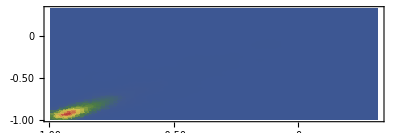

```mathematica
SmoothDensityHistogram[
Out[44],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

```mathematica
PairedHistogram[
Out[44],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

PairedHistogram::argbu: PairedHistogram called with 1 argument; between 2 and 4 arguments are expected.

General::stop: Further output of PairedHistogram::argbu will be suppressed during this calculation.

PairedHistogram[1]
 |  |  |  |

```mathematica
PairedHistogram[
{First/@Out[44],Last/@Out[44]},
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

PairedHistogram::argbu: PairedHistogram called with 1 argument; between 2 and 4 arguments are expected.

General::stop: Further output of PairedHistogram::argbu will be suppressed during this calculation.

PairedHistogram[{{-0.967001,-0.967726,-0.913491,-0.90332,-0.899158,-0.90155,-0.887085,-0.958147,-0.911671,-0.926301,-0.90044,-0.916734,-0.919902,-0.916299,-0.924227,-0.931257,-0.936411,-0.83609,2224,-0.735913,-0.739542,-0.647582,-0.535996,-0.498655,-0.438682,-0.217928,-0.712302,-0.582186,-0.712989,-0.806905,-0.803723,-0.834586,-0.841069,-0.868221,-0.865659,-0.886578},{1}},4,1]
 |  |  |  |

```mathematica
QuantilePlot[
data,
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
BoxWhiskerChart[
FinancialData["VIX","Close",All],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
BoxWhiskerChart[
data,
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
FindClusters[data]
```

{{-0.967001,-0.967726,-0.913491,-0.90332,-0.899158,-0.90155,-0.887085,-0.958147,-0.911671,-0.926301,-0.90044,-0.916734,-0.919902,-0.916299,-0.924227,-0.931257,-0.936411,-0.83609,-0.927461,-0.846194,-0.569167,-0.932261,-0.93298,-0.915744,-0.932461,-0.931214,-0.931024,-0.933285,-0.952746,-0.957513,-0.954938,-0.94475,-0.947561,-0.953827,-0.96024,-0.972594,-0.979241,-0.96139,-0.957795,-0.956161,-0.963499,-0.961174,-0.962711,-0.955099,-0.946973,-0.948503,-0.940219,-0.8187,-0.831383,-0.829511,-0.667713,-0.64979,-0.779211,-0.761544,-0.846368,-0.736694,-0.712335,-0.624412,-0.634392,-0.72547,-0.81861,-0.838034,-0.868666,-0.880645,-0.890822,-0.865603,-0.795445,-0.794302,-0.751245,-0.745215,-0.731454,-0.804532,-0.789664,-0.785967,-0.855638,-0.878273,-0.866882,-0.861011,-0.873584,-0.93103,-0.931378,-0.925707,-0.915979,-0.922562,-0.941091,-0.922002,-0.914133,-0.934068,-0.930188,-0.921981,-0.974239,-0.973372,-0.95013,-0.948147,-0.944784,-0.936017,-0.943027,-0.947034,-0.905066,-0.902077,-0.844862,-0.703208,-0.772034,-0.808365,-0.830653,-0.821179,-0.802704,-0.822856,-0.831379,-0.841501,-0.747367,-0.893064,-0.894714,-0.933241,-0.918737,-0.917288,-0.917282,-0.944729,-0.949789,-0.945155,-0.958445,-0.961756,-0.926893,-0.951493,-0.929336,-0.939622,-0.948339,-0.917996,-0.916797,-0.938383,-0.93828,-0.890758,-0.793055,-0.831199,-0.792884,-0.908135,-0.880575,-0.874196,-0.90933,-0.916813,-0.900207,-0.915255,-0.950087,-0.94734,-0.946987,-0.929853,-0.929775,-0.927258,-0.914047,-0.904893,-0.917102,-0.9184,-0.922102,-0.930757,-0.931161,-0.923641,-0.931614,-0.954161,-0.948812,-0.946558,-0.93614,-0.929523,-0.906029,-0.916255,-0.917891,-0.924986,-0.933836,-0.921304,-0.921386,-0.94484,-0.929036,-0.941883,-0.943611,-0.947029,-0.945028,-0.954637,-0.954369,-0.959421,-0.973672,-0.957499,-0.964105,-0.972822,-0.970396,-0.929668,-0.930359,-0.911144,-0.8806,-0.866881,-0.88304,-0.898613,-0.909498,-0.928862,-0.937519,-0.957327,-0.966574,-0.964946,-0.968203,-0.981365,-0.975698,-0.977183,-0.97629,-0.975068,-0.982027,-0.988675,-0.975356,-0.97215,-0.96519,-0.955213,-0.955258,-0.953859,-0.937812,-0.906007,-0.892933,-0.858075,-0.833217,-0.825743,-0.832678,-0.903319,-0.898769,-0.902055,-0.907149,-0.910239,-0.905626,-0.905736,-0.877628,-0.860961,-0.848805,-0.699131,-0.711996,-0.712156,-0.740951,-0.809577,-0.854788,-0.706074,-0.580836,-0.620684,-0.655392,-0.650433,-0.717807,-0.909786,-0.869967,-0.759498,-0.798614,-0.767198,-0.680965,-0.732557,-0.628565,-0.628982,-0.658069,-0.748875,-0.791702,-0.773776,-0.742901,-0.760406,-0.721935,-0.69596,-0.816111,-0.837025,-0.794261,-0.684821,-0.62287,-0.785975,-0.758913,-0.786154,-0.815656,-0.850086,-0.819483,-0.844004,-0.715343,-0.749351,-0.765471,-0.663023,-0.602689,-0.665466,-0.761561,-0.79345,-0.880402,-0.839288,-0.809988,-0.821305,-0.819673,-0.813354,-0.777119,-0.585,-0.594695,-0.630119,-0.650453,-0.620621,-0.66957,-0.685317,-0.742037,-0.645355,-0.883925,-0.922243,-0.932531,-0.921184,-0.956363,-0.956665,-0.960793,-0.95676,-0.956573,-0.938771,-0.952373,-0.947994,-0.927931,-0.942766,-0.940093,-0.940445,-0.947029,-0.973705,-0.96968,-0.970645,-0.921942,-0.886932,-0.894171,-0.897327,-0.813981,-0.786984,-0.794662,-0.833242,-0.94037,-0.904601,-0.905534,-0.905175,-0.887285,-0.891624,-0.907574,-0.909131,-0.918684,-0.886294,-0.840168,-0.917771,-0.917487,-0.92471,-0.920982,-0.901695,-0.886844,-0.889293,-0.846822,-0.818889,-0.813213,-0.768353,-0.869359,-0.840711,-0.848004,-0.886118,-0.823247,-0.798608,-0.763914,-0.774198,-0.781195,-0.804568,-0.660856,-0.705987,-0.612345,-0.58586,-0.697273,-0.769545,-0.729547,-0.804958,-0.674881,-0.682277,-0.799118,-0.837983,-0.847753,-0.875996,-0.91455,-0.842016,-0.863873,-0.872825,-0.866844,-0.78571,-0.819612,-0.791442,-0.680072,-0.638355,-0.568666,-0.610525,-0.80028,-0.79789,-0.795947,-0.842981,-0.836491,-0.791805,-0.937989,-0.908456,-0.901796,-0.899317,-0.904973,-0.914465,-0.830034,-0.825543,-0.805475,-0.828614,-0.706772,-0.719185,-0.621776,-0.771066,-0.792914,-0.795437,-0.963428,-0.935383,-0.954039,-0.927331,-0.902714,-0.895963,-0.908679,-0.882994,-0.789256,-0.705769,-0.695128,-0.810193,-0.805717,-0.818334,-0.801457,-0.894037,-0.892913,-0.893704,-0.944667,-0.945121,-0.944086,-0.929462,-0.965414,-0.971814,-0.936214,-0.934892,-0.936606,-0.889271,-0.886016,-0.837431,-0.838658,-0.865615,-0.807975,-0.822218,-0.921917,-0.92324,-0.834789,-0.85138,-0.859242,-0.947265,-0.946566,-0.92785,-0.916284,-0.955189,-0.898317,-0.912725,-0.868155,-0.72509,-0.735095,-0.756999,-0.68051,-0.640651,-0.597739,-0.670637,-0.708662,-0.804684,-0.740622,-0.838686,-0.758141,-0.743409,-0.745297,-0.782471,-0.876964,-0.922999,-0.921194,-0.91565,-0.947356,-0.944345,-0.956207,-0.971417,-0.971132,-0.955493,-0.949822,-0.709966,-0.866828,-0.875937,-0.890126,-0.875186,-0.911621,-0.895235,-0.893809,-0.941641,-0.942481,-0.908687,-0.823298,-0.931437,-0.915306,-0.898791,-0.948028,-0.953908,-0.961656,-0.961765,-0.947978,-0.948046,-0.945794,-0.93304,-0.944506,-0.947961,-0.74361,-0.782328,-0.662995,-0.702378,-0.847688,-0.852945,-0.89837,-0.889326,-0.798756,-0.744959,-0.763616,-0.760309,-0.747534,-0.745484,-0.727399,-0.80452,-0.825673,-0.775663,-0.884673,-0.943515,-0.896184,-0.901869,-0.842489,-0.921898,-0.934135,-0.932766,-0.932173,-0.93314,-0.932645,-0.937006,-0.959725,-0.95049,-0.96437,-0.95211,-0.939576,-0.877313,-0.852267,-0.90106,-0.89838,-0.877946,-0.834683,-0.881142,-0.896725,-0.899065,-0.855271,-0.644626,-0.650592,-0.652057,-0.713628,-0.714482,-0.728563,-0.712816,-0.697263,-0.714374,-0.763262,-0.845276,-0.893306,-0.843776,-0.887097,-0.943717,-0.942023,-0.943127,-0.938511,-0.897863,-0.882772,-0.910406,-0.927063,-0.931125,-0.936337,-0.828726,-0.908155,-0.883154,-0.890352,-0.899113,-0.906433,-0.897118,-0.877849,-0.888535,-0.891896,-0.945582,-0.88177,-0.893159,-0.759628,-0.780632,-0.745104,-0.752194,-0.787724,-0.833526,-0.756338,-0.751255,-0.681357,-0.677379,-0.677392,-0.723585,-0.813875,-0.833491,-0.850374,-0.794547,-0.793068,-0.81072,-0.794833,-0.791018,-0.820574,-0.817261,-0.815114,-0.820419,-0.80471,-0.817634,-0.853563,-0.919667,-0.880815,-0.892558,-0.903803,-0.908298,-0.913877,-0.924619,-0.894936,-0.917445,-0.921891,-0.875584,-0.925501,-0.908197,-0.866629,-0.843541,-0.827968,-0.857007,-0.860203,-0.567302,-0.643372,-0.681903,-0.57009,-0.594989,-0.788955,-0.839213,-0.886223,-0.884397,-0.865595,-0.893339,-0.923024,-0.820998,-0.828925,-0.859927,-0.771466,-0.809527,-0.810914,-0.837108,-0.856488,-0.846715,-0.922761,-0.924912,-0.91007,-0.912646,-0.907301,-0.904081,-0.909711,-0.896794,-0.874009,-0.892136,-0.869957,-0.866622,-0.889131,-0.820723,-0.622049,-0.602768,-0.586534,-0.817328,-0.906731,-0.926913,-0.949526,-0.88074,-0.891527,-0.895863,-0.917962,-0.931514,-0.830361,-0.731337,-0.621412,-0.637821,-0.640381,-0.716485,-0.660835,-0.868869,-0.889458,-0.881805,-0.872167,-0.927064,-0.931031,-0.942093,-0.875257,-0.851398,-0.932653,-0.929009,-0.882815,-0.873339,-0.867665,-0.793573,-0.79336,-0.798777,-0.830121,-0.864218,-0.65125,-0.567865,-0.709946,-0.674645,-0.673892,-0.619631,-0.803595,-0.900802,-0.852351,-0.826188,-0.822373,-0.863051,-0.837816,-0.868514,-0.936126,-0.938139,-0.938278,-0.913071,-0.914823,-0.857143,-0.870451,-0.876103,-0.866542,-0.882058,-0.877448,-0.879837,-0.886248,-0.859818,-0.874543,-0.892873,-0.866871,-0.919214,-0.908214,-0.899714,-0.859142,-0.853379,-0.863988,-0.876682,-0.856184,-0.890379,-0.943275,-0.922289,-0.937809,-0.938928,-0.914811,-0.896166,-0.89186,-0.90662,-0.934115,-0.952158,-0.92923,-0.930951,-0.908903,-0.934867,-0.923052,-0.919772,-0.917724,-0.867752,-0.878447,-0.876183,-0.87914,-0.77651,-0.819318,-0.849597,-0.882396,-0.889192,-0.879195,-0.947497,-0.948457,-0.930969,-0.944681,-0.962145,-0.957919,-0.960314,-0.955452,-0.958976,-0.938448,-0.811185,-0.667938,-0.721504,-0.694863,-0.572384,-0.634614,-0.785664,-0.679819,-0.774027,-0.733039,-0.792733,-0.84382,-0.85089,-0.845363,-0.756629,-0.72069,-0.674247,-0.704299,-0.639534,-0.69074,-0.632946,-0.687534,-0.786996,-0.707523,-0.728178,-0.634221,-0.736945,-0.902376,-0.905854,-0.906977,-0.897814,-0.916871,-0.912756,-0.861338,-0.843895,-0.885187,-0.886896,-0.830028,-0.827878,-0.815341,-0.805111,-0.723376,-0.726102,-0.833778,-0.894417,-0.867689,-0.878914,-0.885098,-0.896377,-0.917932,-0.91575,-0.942779,-0.965756,-0.963207,-0.99504,-0.986674,-0.979727,-0.976782,-0.972978,-0.929772,-0.918879,-0.916765,-0.856746,-0.888313,-0.88534,-0.895503,-0.889603,-0.910714,-0.897917,-0.910684,-0.923006,-0.903147,-0.919911,-0.915474,-0.827468,-0.778289,-0.646189,-0.646525,-0.668551,-0.728915,-0.703742,-0.77383,-0.780297,-0.619643,-0.604858,-0.6494,-0.76892,-0.814616,-0.820708,-0.905281,-0.801508,-0.876334,-0.895994,-0.896772,-0.889733,-0.91809,-0.921679,-0.937913,-0.961901,-0.967597,-0.936156,-0.931675,-0.862756,-0.849267,-0.888029,-0.879846,-0.904272,-0.928933,-0.935544,-0.894465,-0.923815,-0.92644,-0.939689,-0.934847,-0.931663,-0.934362,-0.937811,-0.917413,-0.922687,-0.918722,-0.850172,-0.858577,-0.902425,-0.877628,-0.864813,-0.894962,-0.812857,-0.717965,-0.629252,-0.633612,-0.625209,-0.650498,-0.804738,-0.771421,-0.813612,-0.880415,-0.819883,-0.792289,-0.853855,-0.915485,-0.912657,-0.926453,-0.927084,-0.924732,-0.955679,-0.948884,-0.979464,-0.762606,-0.738065,-0.645849,-0.567748,-0.77419,-0.745677,-0.754554,-0.739542,-0.739081,-0.657876,-0.766199,-0.686358,-0.795796,-0.808326,-0.696273,-0.894048,-0.876228,-0.882646,-0.920409,-0.927156,-0.933806,-0.930214,-0.92593,-0.952674,-0.963631,-0.950942,-0.919118,-0.931881,-0.913241,-0.867236,-0.877932,-0.894513,-0.897727,-0.89806,-0.932263,-0.927357,-0.935614,-0.928651,-0.926692,-0.939444,-0.966302,-0.954367,-0.946818,-0.923145,-0.914538,-0.897911,-0.825883,-0.823872,-0.828039,-0.745422,-0.793847,-0.774238,-0.569263,-0.710696,-0.826004,-0.813217,-0.835888,-0.89248,-0.893178,-0.91024,-0.885043,-0.930194,-0.934564,-0.902435,-0.897539,-0.920356,-0.918338,-0.889296,-0.86595,-0.802349,-0.876461,-0.847209,-0.846355,-0.886543,-0.900295,-0.86847,-0.872866,-0.903876,-0.927865,-0.957165,-0.907826,-0.872567,-0.874085,-0.919259,-0.884346,-0.843094,-0.904258,-0.911357,-0.909695,-0.882046,-0.879143,-0.907178,-0.890163,-0.852524,-0.846643,-0.889108,-0.907151,-0.874369,-0.883311,-0.890924,-0.887297,-0.917028,-0.922593,-0.934165,-0.932095,-0.907545,-0.895257,-0.892351,-0.831135,-0.813486,-0.814156,-0.711584,-0.828593,-0.864766,-0.86358,-0.907748,-0.903569,-0.883222,-0.903932,-0.920733,-0.869126,-0.877389,-0.82943,-0.839677,-0.86469,-0.877426,-0.835675,-0.85512,-0.847157,-0.825392,-0.880779,-0.856793,-0.836768,-0.836938,-0.83543,-0.839952,-0.920387,-0.922424,-0.930053,-0.912505,-0.925961,-0.927839,-0.933364,-0.943286,-0.956452,-0.961732,-0.927005,-0.92593,-0.927611,-0.968589,-0.967916,-0.948786,-0.878389,-0.90908,-0.905624,-0.834566,-0.919479,-0.883733,-0.872982,-0.873102,-0.851212,-0.872339,-0.870504,-0.886793,-0.866118,-0.857956,-0.856425,-0.860589,-0.845096,-0.828157,-0.892335,-0.897339,-0.890669,-0.943841,-0.97129,-0.982704,-0.972977,-0.958724,-0.912185,-0.912242,-0.909848,-0.927779,-0.920818,-0.915488,-0.902357,-0.878806,-0.84844,-0.808529,-0.943036,-0.966631,-0.958144,-0.93055,-0.918168,-0.908494,-0.879603,-0.925808,-0.957366,-0.961807,-0.95525,-0.902276,-0.86432,-0.833089,-0.842504,-0.872629,-0.940568,-0.93781,-0.9679,-0.959746,-0.977389,-0.709976,-0.774497,-0.811858,-0.840941,-0.831615,-0.720341,-0.707852,-0.767483,-0.810294,-0.717718,-0.787544,-0.719999,-0.705902,-0.656802,-0.660587,-0.819815,-0.805167,-0.782617,-0.571649,-0.66176,-0.751394,-0.786047,-0.79854,-0.875525,-0.898291,-0.936187,-0.926077,-0.926155,-0.930882,-0.942433,-0.913562,-0.918371,-0.91118,-0.878478,-0.797322,-0.702552,-0.817854,-0.82937,-0.933663,-0.937004,-0.961526,-0.962313,-0.953623,-0.94118,-0.941084,-0.940459,-0.952773,-0.931401,-0.917186,-0.925358,-0.931388,-0.914144,-0.919196,-0.916113,-0.933935,-0.934838,-0.922422,-0.930027,-0.876041,-0.871248,-0.905383,-0.907936,-0.907869,-0.92704,-0.979391,-0.950345,-0.957045,-0.955498,-0.951294,-0.956909,-0.960987,-0.959906,-0.974658,-0.978514,-0.969625,-0.945139,-0.934407,-0.947857,-0.947455,-0.944701,-0.937692,-0.935549,-0.927442,-0.924684,-0.930564,-0.936191,-0.962474,-0.96192,-0.945442,-0.918734,-0.920779,-0.918553,-0.917183,-0.918412,-0.903529,-0.915884,-0.939972,-0.94747,-0.944527,-0.946234,-0.941366,-0.939011,-0.94003,-0.924066,-0.933904,-0.91748,-0.831846,-0.82877,-0.848238,-0.891039,-0.870316,-0.736705,-0.808608,-0.822195,-0.839197,-0.918001,-0.913219,-0.912966,-0.909888,-0.934116,-0.962531,-0.981101,-0.980849,-0.982107,-0.985477,-0.971128,-0.973089,-0.975947,-0.960188,-0.955761,-0.927313,-0.913189,-0.83129,-0.798064,-0.7924,-0.797445,-0.73613,-0.857433,-0.885067,-0.888197,-0.959867,-0.970458,-0.967689,-0.975496,-0.978917,-0.945357,-0.952729,-0.94892,-0.957535,-0.955765,-0.956862,-0.956486,-0.957284,-0.976443,-0.981367,-0.965348,-0.952229,-0.959508,-0.943317,-0.933032,-0.929093,-0.91666,-0.90024,-0.883911,-0.836912,-0.859644,-0.843576,-0.805837,-0.781005,-0.781997,-0.767224,-0.830541,-0.812192,-0.83586,-0.871082,-0.925424,-0.896316,-0.910115,-0.893046,-0.883395,-0.88409,-0.887757,-0.891348,-0.892382,-0.890823,-0.787887,-0.851862,-0.867574,-0.804113,-0.827864,-0.860436,-0.817249,-0.810426,-0.881711,-0.732849,-0.745259,-0.721057,-0.644841,-0.804545,-0.780826,-0.760243,-0.848412,-0.858007,-0.83549,-0.786315,-0.766258,-0.768767,-0.791789,-0.709129,-0.712617,-0.748426,-0.722429,-0.703703,-0.743203,-0.707972,-0.775261,-0.784721,-0.811338,-0.893379,-0.921239,-0.920008,-0.848873,-0.885298,-0.869162,-0.887119,-0.910031,-0.930453,-0.918272,-0.987674,-0.976583,-0.965979,-0.968362,-0.965272,-0.948396,-0.942544,-0.941133,-0.950132,-0.952533,-0.896777,-0.906708,-0.891314,-0.862762,-0.912542,-0.938549,-0.935858,-0.921928,-0.884383,-0.875718,-0.883014,-0.859199,-0.903926,-0.908595,-0.883452,-0.838601,-0.843346,-0.901672,-0.921979,-0.905177,-0.902078,-0.91518,-0.829898,-0.853413,-0.861958,-0.837841,-0.856646,-0.803397,-0.749787,-0.766353,-0.744302,-0.951887,-0.957093,-0.938222,-0.923863,-0.887523,-0.889486,-0.88689,-0.885481,-0.872824,-0.863245,-0.594077,-0.574384,-0.622123,-0.711837,-0.847758,-0.844692,-0.788212,-0.785271,-0.749852,-0.805575,-0.768863,-0.647731,-0.710542,-0.743949,-0.864682,-0.894009,-0.905456,-0.928102,-0.905643,-0.910684,-0.913704,-0.888847,-0.867894,-0.818216,-0.698429,-0.609239,-0.638626,-0.62899,-0.779068,-0.73531,-0.731407,-0.70506,-0.816984,-0.83403,-0.85173,-0.808009,-0.807664,-0.841097,-0.830168,-0.784459,-0.821363,-0.888645,-0.816028,-0.761165,-0.740246,-0.703721,-0.727539,-0.821724,-0.907774,-0.86565,-0.760436,-0.738936,-0.711355,-0.772349,-0.720082,-0.69612,-0.718547,-0.720609,-0.655002,-0.748091,-0.790105,-0.791528,-0.832186,-0.619492,-0.679982,-0.625063,-0.624217,-0.662604,-0.618164,-0.779772,-0.811144,-0.853219,-0.854807,-0.844444,-0.815373,-0.836052,-0.835159,-0.894799,-0.840731,-0.928861,-0.931726,-0.965065,-0.971417,-0.969347,-0.97281,-0.949629,-0.952762,-0.949533,-0.954433,-0.569638,-0.675255,-0.724941,-0.805033,-0.773097,-0.802355,-0.881493,-0.846821,-0.878858,-0.868193,-0.88534,-0.895127,-0.888018,-0.908679,-0.910439,-0.921927,-0.927712,-0.881643,-0.857844,-0.901517,-0.926754,-0.904959,-0.925065,-0.923913,-0.923897,-0.885557,-0.8235,-0.862297,-0.843411,-0.645024,-0.85423,-0.778359,-0.977154,-0.949152,-0.959958,-0.957757,-0.957644,-0.974308,-0.955835,-0.952105,-0.950199,-0.951142,-0.933798,-0.955495,-0.944923,-0.936903,-0.910525,-0.703268,-0.788994,-0.914837,-0.864927,-0.878258,-0.870631,-0.939188,-0.943442,-0.872891,-0.90871,-0.901695,-0.872261,-0.765248,-0.764649,-0.7574,-0.743527,-0.605874,-0.696972,-0.668541,-0.655226,-0.787368,-0.798808,-0.831912,-0.852108,-0.858616,-0.821877,-0.791944,-0.774372,-0.810124,-0.832345,-0.77825,-0.693617,-0.806779,-0.6955,-0.808182,-0.862258,-0.939155,-0.928439,-0.918121,-0.903269,-0.894957,-0.877322,-0.855707,-0.894153,-0.825403,-0.848929,-0.561859,-0.584215,-0.79428,-0.928115,-0.800794,-0.760338,-0.817204,-0.822501,-0.799647,-0.828314,-0.708425,-0.679394,-0.680253,-0.624466,-0.643837,-0.658313,-0.647893,-0.573984,-0.59332,-0.593428,-0.784413,-0.856218,-0.823542,-0.873109,-0.851156,-0.71622,-0.708118,-0.647728,-0.63023,-0.65192,-0.610085,-0.610149,-0.6664,-0.701863,-0.723248,-0.877141,-0.835766,-0.886836,-0.821875,-0.714702,-0.604598,-0.831648,-0.9368,-0.916844,-0.915082,-0.932084,-0.948743,-0.950069,-0.958311,-0.960371,-0.965197,-0.965872,-0.947863,-0.962909,-0.961101,-0.865208,-0.842359,-0.902468,-0.905502,-0.940345,-0.958414,-0.964191,-0.958257,-0.959162,-0.958088,-0.958695,-0.94396,-0.936265,-0.930992,-0.84477,-0.840478,-0.886146,-0.900865,-0.895613,-0.939018,-0.864779,-0.900504,-0.908971,-0.907064,-0.932871,-0.941206,-0.955696,-0.955397,-0.960373,-0.962927,-0.966027,-0.949007,-0.93405,-0.934171,-0.885361,-0.810245,-0.795068,-0.833221,-0.837457,-0.738382,-0.764058,-0.923065,-0.891585,-0.897151,-0.967553,-0.934583,-0.938524,-0.866406,-0.836635,-0.81652,-0.813586,-0.702859,-0.790512,-0.788519,-0.797367,-0.727815,-0.749301,-0.830004,-0.750962,-0.811162,-0.790905,-0.803027,-0.791902,-0.759177,-0.765871,-0.872838,-0.838047,-0.807281,-0.852841,-0.862616,-0.866834,-0.873312,-0.874271,-0.887915,-0.885773,-0.903842,-0.89639,-0.862386,-0.865809,-0.781757,-0.793746,-0.750924,-0.858637,-0.892387,-0.960115,-0.970792,-0.967027,-0.915126,-0.918558,-0.932877,-0.92139,-0.90903,-0.909145,-0.920691,-0.890254,-0.882557,-0.694777,-0.723191,-0.752868,-0.751872,-0.700845,-0.737637,-0.69796,-0.659793,-0.800544,-0.919265,-0.781532,-0.750453,-0.754483,-0.679091,-0.676501,-0.663005,-0.726245,-0.775391,-0.722657,-0.776058,-0.927845,-0.851885,-0.791286,-0.783908,-0.74931,-0.752512,-0.735143,-0.659995,-0.58621,-0.745086,-0.742633,-0.926751,-0.897504,-0.924398,-0.803154,-0.754584,-0.626183,-0.575315,-0.616776,-0.628233,-0.666234,-0.619186,-0.650193,-0.625485,-0.844179,-0.908217,-0.906289,-0.935062,-0.926012,-0.987042,-0.976677,-0.981521,-0.978349,-0.973732,-0.974035,-0.979218,-0.976001,-0.974457,-0.9742,-0.961081,-0.937377,-0.957164,-0.948558,-0.939285,-0.945536,-0.956667,-0.957188,-0.95964,-0.964931,-0.940672,-0.95724,-0.945315,-0.959945,-0.969592,-0.969906,-0.943909,-0.907999,-0.926695,-0.92952,-0.8975,-0.889892,-0.91876,-0.900875,-0.84295,-0.833645,-0.852793,-0.902224,-0.932612,-0.922687,-0.93975,-0.946991,-0.939878,-0.94377,-0.976706,-0.966999,-0.961421,-0.950948,-0.813292,-0.84212,-0.825454,-0.827672,-0.866602,-0.785902,-0.80557,-0.785076,-0.7356,-0.761448,-0.852443,-0.845782,-0.822533,-0.761984,-0.795693,-0.936314,-0.941141,-0.941367,-0.915542,-0.838775,-0.570585,-0.816543,-0.810204,-0.768915,-0.78567,-0.857535,-0.876092,-0.871012,-0.882921,-0.88686,-0.913401,-0.878212,-0.875554,-0.948306,-0.940636,-0.944405,-0.877861,-0.832242,-0.813839,-0.861678,-0.860342,-0.744208,-0.771829,-0.647156,-0.638993,-0.676429,-0.752116,-0.743065,-0.755549,-0.811148,-0.835839,-0.88717,-0.918046,-0.881953,-0.983143,-0.984635,-0.953764,-0.944794,-0.943816,-0.922378,-0.916351,-0.905931,-0.782809,-0.925676,-0.897551,-0.902701,-0.904208,-0.922298,-0.924611,-0.901835,-0.900564,-0.90295,-0.930867,-0.753062,-0.740058,-0.8309,-0.777061,-0.696501,-0.693376,-0.851913,-0.850526,-0.901745,-0.919038,-0.932803,-0.703324,-0.582507,-0.58419,-0.673412,-0.590047,-0.743748,-0.732714,-0.832429,-0.841584,-0.949281,-0.925895,-0.916801,-0.900211,-0.920878,-0.927781,-0.931806,-0.930957,-0.925571,-0.928292,-0.949583,-0.949724,-0.954731,-0.978769,-0.967798,-0.9637,-0.959916,-0.961845,-0.961978,-0.917772,-0.914655,-0.937086,-0.883846,-0.90835,-0.894019,-0.865795,-0.887231,-0.770444,-0.723446,-0.567329,-0.617756,-0.577627,-0.735885,-0.780081,-0.776963,-0.736532,-0.745655,-0.745609,-0.781932,-0.700482,-0.808128,-0.91486,-0.895005,-0.892613,-0.942069,-0.946667,-0.931547,-0.93392,-0.936482,-0.922308,-0.949266,-0.927037,-0.900934,-0.957724,-0.963585,-0.961698,-0.962526,-0.960626,-0.962182,-0.969192,-0.97576,-0.982186,-0.991166,-0.982158,-0.979205,-0.978957,-0.986107,-0.989351,-0.984904,-0.982969,-0.970316,-0.971466,-0.969296,-0.970982,-0.973037,-0.975779,-0.957535,-0.867068,-0.883602,-0.862205,-0.854414,-0.834046,-0.846086,-0.810121,-0.640237,-0.728305,-0.732577,-0.830188,-0.855869,-0.842845,-0.870206,-0.885538,-0.892952,-0.93807,-0.959685,-0.988098,-0.986775,-0.985881,-0.987649,-0.988563,-0.987968,-0.964198,-0.951568,-0.918174,-0.912894,-0.895871,-0.888231,-0.776745,-0.751203,-0.73775,-0.633059,-0.590085,-0.569263,-0.647042,-0.782216,-0.723189,-0.711905,-0.706775,-0.723942,-0.689836,-0.823863,-0.821786,-0.831192,-0.78063,-0.735497,-0.847957,-0.846344,-0.859363,-0.891649,-0.868197,-0.920486,-0.920459,-0.868515,-0.894825,-0.922098,-0.929348,-0.944038,-0.950676,-0.945064,-0.943876,-0.924523,-0.924248,-0.948807,-0.893315,-0.842379,-0.74092,-0.735913,-0.739542,-0.647582,-0.712302,-0.582186,-0.712989,-0.806905,-0.803723,-0.834586,-0.841069,-0.868221,-0.865659,-0.886578,-0.85595},{-0.524509,-0.478493,-0.488393,-0.44563,-0.548427,-0.541789,-0.546876,-0.48135,-0.329063,-0.247217,-0.251655,-0.299865,-0.186298,-0.318157,-0.327227,-0.512985,-0.53262,-0.549034,-0.560007,-0.37981,-0.405474,-0.529226,0.0184704,-0.00191889,-0.362038,-0.405869,-0.452085,-0.549916,-0.546198,-0.1498,-0.11584,-0.102742,-0.058815,-0.141002,0.0764931,-0.0973582,-0.17904,-0.522476,-0.537592,-0.529036,-0.557505,-0.494018,-0.476969,-0.548284,-0.556894,-0.550397,-0.530335,-0.534767,-0.49284,-0.400891,-0.400756,-0.443262,-0.29616,-0.37197,-0.43767,-0.425285,-0.560208,-0.517233,-0.526359,-0.449554,-0.501371,-0.423866,-0.41329,-0.414,-0.404726,-0.345481,-0.28379,-0.114043,-0.073601,0.128135,0.160184,0.0224936,-0.113832,-0.0996859,-0.0889358,-0.436347,-0.42988,-0.402392,-0.263216,-0.265635,-0.368197,-0.272242,-0.22798,-0.209602,-0.422287,-0.52896,-0.380707,-0.268181,-0.361323,-0.374841,-0.464849,-0.477634,-0.467484,-0.51516,-0.400471,-0.316383,-0.450522,-0.360374,-0.289885,-0.299347,-0.282181,-0.347139,-0.336819,-0.550922,-0.486017,-0.539745,-0.542695,-0.474594,-0.507683,-0.429003,-0.468161,-0.250943,0.0115826,-0.169891,-0.168653,-0.260289,-0.320233,-0.147458,-0.295746,-0.385468,-0.560032,-0.452733,-0.450572,-0.49127,-0.547672,-0.3606,-0.342527,-0.410718,-0.446659,-0.293599,-0.345047,-0.420704,-0.405241,-0.424862,-0.305581,-0.485329,-0.548743,-0.458272,-0.43867,-0.51878,-0.437926,-0.488176,-0.430746,0.112859,-0.18056,-0.112393,-0.128377,-0.279625,-0.462385,-0.495985,-0.518758,-0.532181,-0.091441,0.108414,0.316931,-0.141839,-0.090791,-0.454985,-0.45274,-0.469936,-0.50925,-0.448805,-0.512034,-0.535996,-0.498655,-0.438682,-0.217928}}

```mathematica
FindDistribution[data]
```

FrechetDistribution[2.2016,0.15549,-1.06237]

```mathematica
PDF[FrechetDistribution[2.201595541612302,0.15549047234097954,-1.06236956131618],x]
```

Piecewise[{{(0.036576 ⅇ^(-0.0166134/(1.06237+x)^2.2016))/(1.06237+x)^3.2016, x>-1.06237}, {0, True}}]

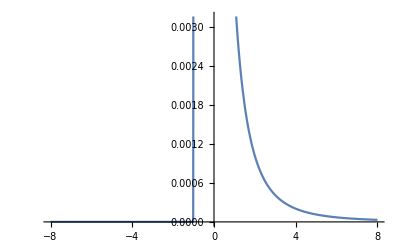

```mathematica
Plot[Piecewise[{{(0.03657599834588616 ⅇ^(-0.01661340498495938/(1.06236956131618+x)^2.201595541612302))/(1.06236956131618+x)^3.201595541612302,x>-1.06236956131618}},0],{x,-8,8}]
```

```mathematica
CharacteristicFunction[FrechetDistribution[2.201595541612302,0.15549047234097954,-1.06236956131618],x]
```

CharacteristicFunction[FrechetDistribution[2.2016,0.15549,-1.06237],x]

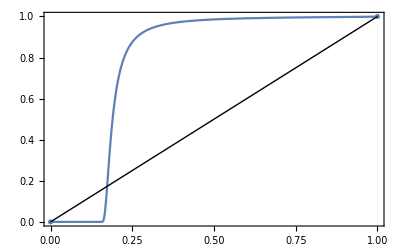

```mathematica
ProbabilityPlot[FrechetDistribution[2.201595541612302,0.15549047234097954,-1.06236956131618]]
```

```mathematica
FindDistribution[data]
```

FrechetDistribution[2.2016,0.15549,-1.06237]

```mathematica
FindDistribution[data[[-10;;]]]
```

MixtureDistribution[{0.656506,0.343494},{NormalDistribution[-0.850673,0.0282708],UniformDistribution[{-0.886578,-0.582186}]}]

```mathematica
PDF[MixtureDistribution[{0.6565063162310059,0.34349368376899403},{NormalDistribution[-0.8506732116233684,0.028270821147423256],UniformDistribution[{-0.8865781934591059,-0.5821863071840658}]}],x]
```

Piecewise[{{0.+9.26426 ⅇ^(-625.595 (0.850673+x)^2), x>-0.582186||x<-0.886578}, {1.12846+9.26426 ⅇ^(-625.595 (0.850673+x)^2), True}}]

General::munfl: Exp[-826.263] is too small to represent as a normalized machine number; precision may be lost.

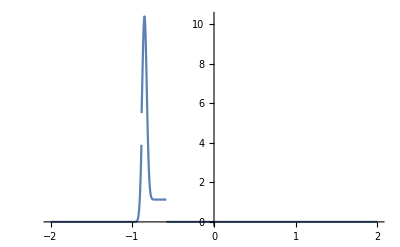

```mathematica
Plot[Out[62],{x,-2,2},PlotRange->Full]
```

```mathematica
Differences@FinancialData["^SPX","Close",All]["Values"]
```

{0.190001,0.0799999,0.0499992,0.1,-0.0499992,0.0599995,-0.33,-0.0900002,0.0499992,0.140001,-0.0100002,0.0200005,0.0299988,0.0200005,-0.0599995,-0.120001,-0.0100002,0.0900002,0.200001,0.0299988,0.,17483,-4.89014,-7.79004,-32.8,-26.8198,-21.51,-87.3101,37.03,2.20996,54.1101,-19.4402,-35.95,43.6201,-85.72,7.,41.0798,34.97,-23.1399,23.9199,-1.47998,-75.8398,31.2698}
 |  |  |  |

```mathematica
Map[
If[#<0,Abs[#]/2,#]&,
Out[64]
]
```

{0.190001,0.0799999,0.0499992,0.1,0.0249996,0.0599995,0.165,0.0450001,0.0499992,0.140001,0.00500011,0.0200005,0.0299988,0.0200005,0.0299997,0.0600004,0.00500011,0.0900002,0.200001,0.0299988,0.,17483,2.44507,3.89502,16.4,13.4099,10.755,43.655,37.03,2.20996,54.1101,9.72009,17.975,43.6201,42.86,7.,41.0798,34.97,11.5699,23.9199,0.73999,37.9199,31.2698}
 |  |  |  |

```mathematica
Accumulate[Out[65]]
```

{0.190001,0.27,0.32,0.42,0.445,0.504999,0.669999,0.714999,0.764998,0.905,0.91,0.93,0.959999,0.98,1.01,1.07,1.075,1.165,1.365,1.395,17485,55481.7,55498.1,55511.5,55522.2,55565.9,55602.9,55605.1,55659.2,55669.,55686.9,55730.5,55773.4,55780.4,55821.5,55856.5,55868.,55891.9,55892.7,55930.6,55961.9}
 |  |  |  |

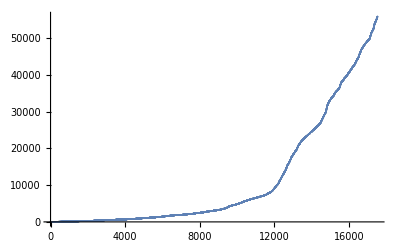

```mathematica
ListPlot[%66]
```

```mathematica
Grid@
Table[
{f,f[data]}
,{f,{Min,Max,Max@#-Min@#&,Commonest,Mean,TrimmedMean,Quartiles,MedianDeviation,StandardDeviation,MeanDeviation,Variance,TrimmedVariance,QuartileDeviation,InterquartileRange,Skewness,QuartileDeviation,Kurtosis,Composition[N,Entropy]}}]
```

Min | -0.99504
Max | 0.316931
Max[#1]-Min[#1]& | 1.31197
Commonest | {-0.967001,-0.967726,-0.913491,-0.90332,-0.899158,-0.90155,-0.887085,-0.958147,-0.911671,-0.926301,-0.90044,-0.916734,-0.919902,-0.916299,-0.924227,-0.931257,-0.936411,-0.83609,-0.927461,-0.846194,-0.524509,-0.478493,-0.569167,-0.932261,-0.93298,-0.915744,-0.932461,-0.931214,-0.931024,-0.933285,-0.952746,-0.957513,-0.954938,-0.94475,-0.947561,-0.953827,-0.96024,-0.972594,-0.979241,-0.96139,-0.957795,-0.956161,-0.963499,-0.961174,-0.962711,-0.955099,-0.946973,-0.948503,-0.940219,-0.8187,-0.831383,-0.829511,-0.667713,-0.64979,-0.779211,-0.761544,-0.846368,-0.736694,-0.712335,-0.624412,-0.634392,-0.72547,-0.81861,-0.838034,-0.868666,-0.880645,-0.890822,-0.865603,-0.795445,-0.794302,-0.751245,-0.745215,-0.731454,-0.804532,-0.789664,-0.785967,-0.855638,-0.878273,-0.866882,-0.861011,-0.873584,-0.93103,-0.931378,-0.925707,-0.915979,-0.922562,-0.941091,-0.922002,-0.914133,-0.934068,-0.930188,-0.921981,-0.974239,-0.973372,-0.95013,-0.948147,-0.944784,-0.936017,-0.943027,-0.947034,-0.905066,-0.902077,-0.844862,-0.703208,-0.772034,-0.808365,-0.830653,-0.821179,-0.802704,-0.822856,-0.831379,-0.841501,-0.747367,-0.893064,-0.894714,-0.933241,-0.918737,-0.917288,-0.917282,-0.944729,-0.949789,-0.945155,-0.958445,-0.961756,-0.926893,-0.951493,-0.929336,-0.939622,-0.948339,-0.917996,-0.916797,-0.938383,-0.93828,-0.890758,-0.793055,-0.831199,-0.792884,-0.908135,-0.880575,-0.874196,-0.90933,-0.916813,-0.900207,-0.915255,-0.950087,-0.94734,-0.946987,-0.929853,-0.929775,-0.927258,-0.914047,-0.904893,-0.917102,-0.9184,-0.922102,-0.930757,-0.931161,-0.923641,-0.931614,-0.954161,-0.948812,-0.946558,-0.93614,-0.929523,-0.906029,-0.916255,-0.917891,-0.924986,-0.933836,-0.921304,-0.921386,-0.94484,-0.929036,-0.941883,-0.943611,-0.947029,-0.945028,-0.954637,-0.954369,-0.959421,-0.973672,-0.957499,-0.964105,-0.972822,-0.970396,-0.929668,-0.930359,-0.911144,-0.8806,-0.866881,-0.88304,-0.898613,-0.909498,-0.928862,-0.937519,-0.957327,-0.966574,-0.964946,-0.968203,-0.981365,-0.975698,-0.977183,-0.97629,-0.975068,-0.982027,-0.988675,-0.975356,-0.97215,-0.96519,-0.955213,-0.955258,-0.953859,-0.937812,-0.906007,-0.892933,-0.858075,-0.833217,-0.825743,-0.832678,-0.903319,-0.898769,-0.902055,-0.907149,-0.910239,-0.905626,-0.905736,-0.877628,-0.860961,-0.848805,-0.699131,-0.711996,-0.712156,-0.740951,-0.809577,-0.854788,-0.706074,-0.488393,-0.44563,-0.548427,-0.541789,-0.580836,-0.620684,-0.655392,-0.546876,-0.650433,-0.717807,-0.909786,-0.869967,-0.759498,-0.798614,-0.767198,-0.680965,-0.732557,-0.628565,-0.628982,-0.658069,-0.748875,-0.791702,-0.773776,-0.742901,-0.760406,-0.721935,-0.69596,-0.816111,-0.837025,-0.794261,-0.684821,-0.62287,-0.785975,-0.758913,-0.786154,-0.815656,-0.850086,-0.819483,-0.844004,-0.715343,-0.749351,-0.765471,-0.663023,-0.602689,-0.48135,-0.329063,-0.247217,-0.251655,-0.665466,-0.761561,-0.79345,-0.880402,-0.839288,-0.809988,-0.821305,-0.819673,-0.813354,-0.777119,-0.299865,-0.186298,-0.318157,-0.327227,-0.512985,-0.585,-0.594695,-0.630119,-0.650453,-0.53262,-0.620621,-0.66957,-0.685317,-0.742037,-0.645355,-0.883925,-0.922243,-0.932531,-0.921184,-0.956363,-0.956665,-0.960793,-0.95676,-0.956573,-0.938771,-0.952373,-0.947994,-0.927931,-0.942766,-0.940093,-0.940445,-0.947029,-0.973705,-0.96968,-0.970645,-0.921942,-0.886932,-0.894171,-0.897327,-0.813981,-0.786984,-0.794662,-0.833242,-0.94037,-0.904601,-0.905534,-0.905175,-0.887285,-0.891624,-0.907574,-0.909131,-0.918684,-0.886294,-0.840168,-0.917771,-0.917487,-0.92471,-0.920982,-0.901695,-0.886844,-0.889293,-0.846822,-0.818889,-0.813213,-0.768353,-0.869359,-0.840711,-0.848004,-0.886118,-0.823247,-0.798608,-0.763914,-0.774198,-0.781195,-0.804568,-0.660856,-0.705987,-0.612345,-0.58586,-0.697273,-0.769545,-0.729547,-0.804958,-0.674881,-0.682277,-0.799118,-0.837983,-0.847753,-0.875996,-0.91455,-0.842016,-0.863873,-0.872825,-0.866844,-0.78571,-0.819612,-0.791442,-0.680072,-0.638355,-0.549034,-0.568666,-0.560007,-0.37981,-0.405474,-0.529226,0.0184704,-0.00191889,-0.362038,-0.405869,-0.452085,-0.549916,-0.610525,-0.80028,-0.79789,-0.795947,-0.842981,-0.836491,-0.791805,-0.937989,-0.908456,-0.901796,-0.899317,-0.904973,-0.914465,-0.830034,-0.825543,-0.805475,-0.828614,-0.706772,-0.719185,-0.621776,-0.771066,-0.792914,-0.795437,-0.963428,-0.935383,-0.954039,-0.927331,-0.902714,-0.895963,-0.908679,-0.882994,-0.789256,-0.705769,-0.695128,-0.810193,-0.805717,-0.818334,-0.801457,-0.894037,-0.892913,-0.893704,-0.944667,-0.945121,-0.944086,-0.929462,-0.965414,-0.971814,-0.936214,-0.934892,-0.936606,-0.889271,-0.886016,-0.837431,-0.838658,-0.865615,-0.807975,-0.822218,-0.921917,-0.92324,-0.834789,-0.85138,-0.859242,-0.947265,-0.946566,-0.92785,-0.916284,-0.955189,-0.898317,-0.912725,-0.868155,-0.72509,-0.735095,-0.756999,-0.68051,-0.640651,-0.597739,-0.670637,-0.708662,-0.804684,-0.740622,-0.838686,-0.758141,-0.743409,-0.745297,-0.782471,-0.876964,-0.922999,-0.921194,-0.91565,-0.947356,-0.944345,-0.956207,-0.971417,-0.971132,-0.955493,-0.949822,-0.546198,-0.1498,-0.11584,-0.102742,-0.058815,-0.141002,0.0764931,-0.0973582,-0.17904,-0.522476,-0.537592,-0.709966,-0.866828,-0.875937,-0.890126,-0.875186,-0.911621,-0.895235,-0.893809,-0.941641,-0.942481,-0.908687,-0.823298,-0.931437,-0.915306,-0.898791,-0.948028,-0.953908,-0.961656,-0.961765,-0.947978,-0.948046,-0.945794,-0.93304,-0.944506,-0.947961,-0.74361,-0.782328,-0.662995,-0.529036,-0.702378,-0.847688,-0.852945,-0.89837,-0.889326,-0.798756,-0.744959,-0.763616,-0.760309,-0.747534,-0.745484,-0.727399,-0.80452,-0.825673,-0.775663,-0.884673,-0.943515,-0.896184,-0.901869,-0.842489,-0.921898,-0.934135,-0.932766,-0.932173,-0.93314,-0.932645,-0.937006,-0.959725,-0.95049,-0.96437,-0.95211,-0.939576,-0.877313,-0.852267,-0.90106,-0.89838,-0.877946,-0.834683,-0.881142,-0.896725,-0.899065,-0.855271,-0.644626,-0.650592,-0.652057,-0.713628,-0.714482,-0.728563,-0.712816,-0.697263,-0.714374,-0.763262,-0.845276,-0.893306,-0.843776,-0.887097,-0.943717,-0.942023,-0.943127,-0.938511,-0.897863,-0.882772,-0.910406,-0.927063,-0.931125,-0.936337,-0.828726,-0.908155,-0.883154,-0.890352,-0.899113,-0.906433,-0.897118,-0.877849,-0.888535,-0.891896,-0.945582,-0.88177,-0.893159,-0.759628,-0.780632,-0.745104,-0.752194,-0.787724,-0.833526,-0.756338,-0.751255,-0.681357,-0.677379,-0.677392,-0.723585,-0.813875,-0.833491,-0.850374,-0.794547,-0.793068,-0.81072,-0.794833,-0.791018,-0.820574,-0.817261,-0.815114,-0.820419,-0.80471,-0.817634,-0.853563,-0.919667,-0.880815,-0.892558,-0.903803,-0.908298,-0.913877,-0.924619,-0.894936,-0.917445,-0.921891,-0.875584,-0.925501,-0.908197,-0.866629,-0.843541,-0.827968,-0.857007,-0.860203,-0.567302,-0.643372,-0.681903,-0.57009,-0.594989,-0.788955,-0.839213,-0.886223,-0.884397,-0.865595,-0.893339,-0.923024,-0.820998,-0.828925,-0.859927,-0.771466,-0.809527,-0.810914,-0.837108,-0.856488,-0.846715,-0.922761,-0.924912,-0.91007,-0.912646,-0.907301,-0.904081,-0.909711,-0.896794,-0.874009,-0.892136,-0.869957,-0.866622,-0.889131,-0.820723,-0.622049,-0.557505,-0.494018,-0.476969,-0.602768,-0.586534,-0.817328,-0.906731,-0.926913,-0.949526,-0.88074,-0.891527,-0.895863,-0.917962,-0.931514,-0.830361,-0.731337,-0.548284,-0.556894,-0.550397,-0.621412,-0.637821,-0.640381,-0.716485,-0.660835,-0.868869,-0.889458,-0.881805,-0.872167,-0.927064,-0.931031,-0.942093,-0.875257,-0.851398,-0.932653,-0.929009,-0.882815,-0.873339,-0.867665,-0.793573,-0.79336,-0.798777,-0.830121,-0.864218,-0.65125,-0.567865,-0.709946,-0.674645,-0.673892,-0.619631,-0.803595,-0.900802,-0.852351,-0.826188,-0.822373,-0.863051,-0.837816,-0.868514,-0.936126,-0.938139,-0.938278,-0.913071,-0.914823,-0.857143,-0.870451,-0.876103,-0.866542,-0.882058,-0.877448,-0.879837,-0.886248,-0.859818,-0.874543,-0.892873,-0.866871,-0.919214,-0.908214,-0.899714,-0.859142,-0.853379,-0.863988,-0.876682,-0.856184,-0.890379,-0.943275,-0.922289,-0.937809,-0.938928,-0.914811,-0.896166,-0.89186,-0.90662,-0.934115,-0.952158,-0.92923,-0.930951,-0.908903,-0.934867,-0.923052,-0.919772,-0.917724,-0.867752,-0.878447,-0.876183,-0.87914,-0.77651,-0.819318,-0.849597,-0.882396,-0.889192,-0.879195,-0.947497,-0.948457,-0.930969,-0.944681,-0.962145,-0.957919,-0.960314,-0.955452,-0.958976,-0.938448,-0.811185,-0.667938,-0.721504,-0.694863,-0.530335,-0.534767,-0.49284,-0.572384,-0.634614,-0.785664,-0.679819,-0.774027,-0.733039,-0.792733,-0.84382,-0.85089,-0.845363,-0.756629,-0.72069,-0.674247,-0.704299,-0.639534,-0.69074,-0.632946,-0.400891,-0.400756,-0.443262,-0.687534,-0.786996,-0.707523,-0.728178,-0.634221,-0.736945,-0.902376,-0.905854,-0.906977,-0.897814,-0.916871,-0.912756,-0.861338,-0.843895,-0.885187,-0.886896,-0.830028,-0.827878,-0.815341,-0.805111,-0.723376,-0.726102,-0.833778,-0.894417,-0.867689,-0.878914,-0.885098,-0.896377,-0.917932,-0.91575,-0.942779,-0.965756,-0.963207,-0.99504,-0.986674,-0.979727,-0.976782,-0.972978,-0.929772,-0.918879,-0.916765,-0.856746,-0.888313,-0.88534,-0.895503,-0.889603,-0.910714,-0.897917,-0.910684,-0.923006,-0.903147,-0.919911,-0.915474,-0.827468,-0.778289,-0.646189,-0.646525,-0.668551,-0.728915,-0.703742,-0.77383,-0.780297,-0.619643,-0.29616,-0.37197,-0.604858,-0.6494,-0.76892,-0.814616,-0.820708,-0.905281,-0.801508,-0.876334,-0.895994,-0.896772,-0.889733,-0.91809,-0.921679,-0.937913,-0.961901,-0.967597,-0.936156,-0.931675,-0.862756,-0.849267,-0.888029,-0.879846,-0.904272,-0.928933,-0.935544,-0.894465,-0.923815,-0.92644,-0.939689,-0.934847,-0.931663,-0.934362,-0.937811,-0.917413,-0.922687,-0.918722,-0.850172,-0.858577,-0.902425,-0.877628,-0.864813,-0.894962,-0.812857,-0.717965,-0.629252,-0.633612,-0.625209,-0.43767,-0.425285,-0.560208,-0.517233,-0.526359,-0.650498,-0.804738,-0.771421,-0.813612,-0.880415,-0.819883,-0.792289,-0.853855,-0.915485,-0.912657,-0.926453,-0.927084,-0.924732,-0.955679,-0.948884,-0.979464,-0.762606,-0.738065,-0.645849,-0.567748,-0.77419,-0.745677,-0.754554,-0.739542,-0.739081,-0.657876,-0.766199,-0.686358,-0.795796,-0.808326,-0.696273,-0.894048,-0.876228,-0.882646,-0.920409,-0.927156,-0.933806,-0.930214,-0.92593,-0.952674,-0.963631,-0.950942,-0.919118,-0.931881,-0.913241,-0.867236,-0.877932,-0.894513,-0.897727,-0.89806,-0.932263,-0.927357,-0.935614,-0.928651,-0.926692,-0.939444,-0.966302,-0.954367,-0.946818,-0.923145,-0.914538,-0.897911,-0.825883,-0.823872,-0.828039,-0.745422,-0.793847,-0.774238,-0.569263,-0.710696,-0.826004,-0.813217,-0.835888,-0.89248,-0.893178,-0.91024,-0.885043,-0.930194,-0.934564,-0.902435,-0.897539,-0.920356,-0.918338,-0.889296,-0.86595,-0.802349,-0.876461,-0.847209,-0.846355,-0.886543,-0.900295,-0.86847,-0.872866,-0.903876,-0.927865,-0.957165,-0.907826,-0.872567,-0.874085,-0.919259,-0.884346,-0.843094,-0.904258,-0.911357,-0.909695,-0.882046,-0.879143,-0.907178,-0.890163,-0.852524,-0.846643,-0.889108,-0.907151,-0.874369,-0.883311,-0.890924,-0.887297,-0.917028,-0.922593,-0.934165,-0.932095,-0.907545,-0.895257,-0.892351,-0.831135,-0.813486,-0.814156,-0.711584,-0.828593,-0.864766,-0.86358,-0.907748,-0.903569,-0.883222,-0.903932,-0.920733,-0.869126,-0.877389,-0.82943,-0.839677,-0.86469,-0.877426,-0.835675,-0.85512,-0.847157,-0.825392,-0.880779,-0.856793,-0.836768,-0.836938,-0.83543,-0.839952,-0.920387,-0.922424,-0.930053,-0.912505,-0.925961,-0.927839,-0.933364,-0.943286,-0.956452,-0.961732,-0.927005,-0.92593,-0.927611,-0.968589,-0.967916,-0.948786,-0.878389,-0.90908,-0.905624,-0.834566,-0.919479,-0.883733,-0.872982,-0.873102,-0.851212,-0.872339,-0.870504,-0.886793,-0.866118,-0.857956,-0.856425,-0.860589,-0.845096,-0.828157,-0.892335,-0.897339,-0.890669,-0.943841,-0.97129,-0.982704,-0.972977,-0.958724,-0.912185,-0.912242,-0.909848,-0.927779,-0.920818,-0.915488,-0.902357,-0.878806,-0.84844,-0.808529,-0.943036,-0.966631,-0.958144,-0.93055,-0.918168,-0.908494,-0.879603,-0.925808,-0.957366,-0.961807,-0.95525,-0.902276,-0.86432,-0.833089,-0.842504,-0.872629,-0.940568,-0.93781,-0.9679,-0.959746,-0.977389,-0.709976,-0.774497,-0.811858,-0.840941,-0.831615,-0.720341,-0.707852,-0.767483,-0.810294,-0.717718,-0.787544,-0.719999,-0.705902,-0.656802,-0.660587,-0.819815,-0.805167,-0.782617,-0.571649,-0.66176,-0.751394,-0.786047,-0.79854,-0.875525,-0.898291,-0.936187,-0.926077,-0.926155,-0.930882,-0.942433,-0.913562,-0.918371,-0.91118,-0.878478,-0.797322,-0.702552,-0.817854,-0.82937,-0.933663,-0.937004,-0.961526,-0.962313,-0.953623,-0.94118,-0.941084,-0.940459,-0.952773,-0.931401,-0.917186,-0.925358,-0.931388,-0.914144,-0.919196,-0.916113,-0.933935,-0.934838,-0.922422,-0.930027,-0.876041,-0.871248,-0.905383,-0.907936,-0.907869,-0.92704,-0.979391,-0.950345,-0.957045,-0.955498,-0.951294,-0.956909,-0.960987,-0.959906,-0.974658,-0.978514,-0.969625,-0.945139,-0.934407,-0.947857,-0.947455,-0.944701,-0.937692,-0.935549,-0.927442,-0.924684,-0.930564,-0.936191,-0.962474,-0.96192,-0.945442,-0.918734,-0.920779,-0.918553,-0.917183,-0.918412,-0.903529,-0.915884,-0.939972,-0.94747,-0.944527,-0.946234,-0.941366,-0.939011,-0.94003,-0.924066,-0.933904,-0.91748,-0.831846,-0.82877,-0.848238,-0.891039,-0.870316,-0.736705,-0.808608,-0.822195,-0.839197,-0.918001,-0.913219,-0.912966,-0.909888,-0.934116,-0.962531,-0.981101,-0.980849,-0.982107,-0.985477,-0.971128,-0.973089,-0.975947,-0.960188,-0.955761,-0.927313,-0.913189,-0.83129,-0.798064,-0.7924,-0.797445,-0.73613,-0.857433,-0.885067,-0.888197,-0.959867,-0.970458,-0.967689,-0.975496,-0.978917,-0.945357,-0.952729,-0.94892,-0.957535,-0.955765,-0.956862,-0.956486,-0.957284,-0.976443,-0.981367,-0.965348,-0.952229,-0.959508,-0.943317,-0.933032,-0.929093,-0.91666,-0.90024,-0.883911,-0.836912,-0.449554,-0.501371,-0.859644,-0.843576,-0.805837,-0.781005,-0.781997,-0.767224,-0.830541,-0.812192,-0.83586,-0.871082,-0.925424,-0.896316,-0.910115,-0.893046,-0.883395,-0.88409,-0.887757,-0.891348,-0.892382,-0.890823,-0.787887,-0.851862,-0.867574,-0.804113,-0.827864,-0.860436,-0.817249,-0.810426,-0.881711,-0.732849,-0.745259,-0.721057,-0.644841,-0.804545,-0.780826,-0.760243,-0.848412,-0.858007,-0.83549,-0.786315,-0.766258,-0.768767,-0.791789,-0.709129,-0.712617,-0.748426,-0.722429,-0.703703,-0.743203,-0.707972,-0.775261,-0.784721,-0.811338,-0.893379,-0.921239,-0.920008,-0.848873,-0.885298,-0.869162,-0.887119,-0.910031,-0.930453,-0.918272,-0.987674,-0.976583,-0.965979,-0.968362,-0.965272,-0.948396,-0.942544,-0.941133,-0.950132,-0.952533,-0.896777,-0.906708,-0.891314,-0.862762,-0.912542,-0.938549,-0.935858,-0.921928,-0.884383,-0.875718,-0.883014,-0.859199,-0.903926,-0.908595,-0.883452,-0.838601,-0.843346,-0.901672,-0.921979,-0.905177,-0.902078,-0.91518,-0.829898,-0.853413,-0.861958,-0.837841,-0.856646,-0.803397,-0.749787,-0.766353,-0.744302,-0.951887,-0.957093,-0.938222,-0.923863,-0.887523,-0.889486,-0.88689,-0.885481,-0.872824,-0.863245,-0.594077,-0.574384,-0.622123,-0.711837,-0.847758,-0.844692,-0.788212,-0.785271,-0.749852,-0.805575,-0.768863,-0.423866,-0.41329,-0.414,-0.404726,-0.345481,-0.28379,-0.114043,-0.073601,0.128135,0.160184,0.0224936,-0.113832,-0.0996859,-0.0889358,-0.647731,-0.710542,-0.743949,-0.864682,-0.894009,-0.905456,-0.928102,-0.905643,-0.910684,-0.913704,-0.888847,-0.867894,-0.818216,-0.698429,-0.609239,-0.638626,-0.62899,-0.779068,-0.73531,-0.731407,-0.70506,-0.816984,-0.83403,-0.85173,-0.808009,-0.807664,-0.841097,-0.830168,-0.784459,-0.821363,-0.888645,-0.816028,-0.761165,-0.436347,-0.42988,-0.402392,-0.263216,-0.265635,-0.368197,-0.272242,-0.22798,-0.209602,-0.422287,-0.52896,-0.380707,-0.268181,-0.361323,-0.374841,-0.464849,-0.477634,-0.467484,-0.51516,-0.740246,-0.703721,-0.727539,-0.821724,-0.907774,-0.86565,-0.760436,-0.738936,-0.711355,-0.772349,-0.720082,-0.69612,-0.718547,-0.720609,-0.655002,-0.748091,-0.790105,-0.791528,-0.832186,-0.619492,-0.400471,-0.316383,-0.679982,-0.625063,-0.624217,-0.662604,-0.618164,-0.779772,-0.811144,-0.853219,-0.854807,-0.844444,-0.815373,-0.836052,-0.835159,-0.894799,-0.840731,-0.450522,-0.360374,-0.289885,-0.299347,-0.282181,-0.347139,-0.336819,-0.928861,-0.931726,-0.965065,-0.971417,-0.969347,-0.97281,-0.949629,-0.952762,-0.949533,-0.954433,-0.569638,-0.550922,-0.486017,-0.539745,-0.542695,-0.474594,-0.675255,-0.724941,-0.805033,-0.773097,-0.802355,-0.881493,-0.846821,-0.878858,-0.868193,-0.88534,-0.895127,-0.888018,-0.908679,-0.910439,-0.921927,-0.927712,-0.881643,-0.857844,-0.901517,-0.926754,-0.904959,-0.925065,-0.923913,-0.923897,-0.885557,-0.8235,-0.862297,-0.843411,-0.507683,-0.429003,-0.468161,-0.250943,0.0115826,-0.169891,-0.168653,-0.260289,-0.320233,-0.147458,-0.295746,-0.385468,-0.645024,-0.85423,-0.778359,-0.977154,-0.949152,-0.959958,-0.957757,-0.957644,-0.974308,-0.955835,-0.952105,-0.950199,-0.951142,-0.933798,-0.955495,-0.944923,-0.936903,-0.910525,-0.703268,-0.788994,-0.914837,-0.864927,-0.878258,-0.870631,-0.939188,-0.943442,-0.872891,-0.90871,-0.901695,-0.872261,-0.765248,-0.764649,-0.7574,-0.743527,-0.605874,-0.560032,-0.452733,-0.450572,-0.49127,-0.696972,-0.668541,-0.655226,-0.787368,-0.798808,-0.831912,-0.852108,-0.858616,-0.821877,-0.791944,-0.774372,-0.810124,-0.832345,-0.77825,-0.693617,-0.806779,-0.6955,-0.808182,-0.862258,-0.939155,-0.928439,-0.918121,-0.903269,-0.894957,-0.877322,-0.855707,-0.894153,-0.825403,-0.848929,-0.561859,-0.547672,-0.584215,-0.79428,-0.928115,-0.800794,-0.760338,-0.817204,-0.822501,-0.799647,-0.828314,-0.708425,-0.679394,-0.3606,-0.342527,-0.410718,-0.446659,-0.293599,-0.345047,-0.420704,-0.405241,-0.424862,-0.305581,-0.485329,-0.680253,-0.624466,-0.643837,-0.658313,-0.647893,-0.573984,-0.59332,-0.593428,-0.784413,-0.856218,-0.823542,-0.873109,-0.851156,-0.71622,-0.708118,-0.647728,-0.548743,-0.458272,-0.43867,-0.63023,-0.65192,-0.610085,-0.610149,-0.6664,-0.701863,-0.723248,-0.877141,-0.835766,-0.886836,-0.821875,-0.714702,-0.604598,-0.831648,-0.9368,-0.916844,-0.915082,-0.932084,-0.948743,-0.950069,-0.958311,-0.960371,-0.965197,-0.965872,-0.947863,-0.962909,-0.961101,-0.865208,-0.842359,-0.902468,-0.905502,-0.940345,-0.958414,-0.964191,-0.958257,-0.959162,-0.958088,-0.958695,-0.94396,-0.936265,-0.930992,-0.84477,-0.840478,-0.886146,-0.900865,-0.895613,-0.939018,-0.864779,-0.900504,-0.908971,-0.907064,-0.932871,-0.941206,-0.955696,-0.955397,-0.960373,-0.962927,-0.966027,-0.949007,-0.93405,-0.934171,-0.885361,-0.810245,-0.795068,-0.833221,-0.837457,-0.738382,-0.764058,-0.923065,-0.891585,-0.897151,-0.967553,-0.934583,-0.938524,-0.866406,-0.836635,-0.81652,-0.813586,-0.702859,-0.790512,-0.788519,-0.797367,-0.727815,-0.749301,-0.830004,-0.750962,-0.811162,-0.790905,-0.803027,-0.791902,-0.759177,-0.765871,-0.872838,-0.838047,-0.807281,-0.852841,-0.862616,-0.866834,-0.873312,-0.874271,-0.887915,-0.885773,-0.903842,-0.89639,-0.862386,-0.865809,-0.781757,-0.793746,-0.750924,-0.858637,-0.892387,-0.960115,-0.970792,-0.967027,-0.915126,-0.918558,-0.932877,-0.92139,-0.90903,-0.909145,-0.920691,-0.890254,-0.882557,-0.694777,-0.723191,-0.752868,-0.751872,-0.700845,-0.737637,-0.69796,-0.51878,-0.437926,-0.659793,-0.800544,-0.919265,-0.781532,-0.750453,-0.754483,-0.679091,-0.676501,-0.663005,-0.726245,-0.775391,-0.722657,-0.776058,-0.927845,-0.851885,-0.791286,-0.783908,-0.74931,-0.752512,-0.735143,-0.659995,-0.488176,-0.430746,0.112859,-0.18056,-0.112393,-0.128377,-0.279625,-0.462385,-0.58621,-0.495985,-0.745086,-0.742633,-0.926751,-0.897504,-0.924398,-0.803154,-0.754584,-0.626183,-0.575315,-0.616776,-0.628233,-0.666234,-0.619186,-0.650193,-0.518758,-0.625485,-0.844179,-0.908217,-0.906289,-0.935062,-0.926012,-0.987042,-0.976677,-0.981521,-0.978349,-0.973732,-0.974035,-0.979218,-0.976001,-0.974457,-0.9742,-0.961081,-0.937377,-0.957164,-0.948558,-0.939285,-0.945536,-0.956667,-0.957188,-0.95964,-0.964931,-0.940672,-0.95724,-0.945315,-0.959945,-0.969592,-0.969906,-0.943909,-0.907999,-0.926695,-0.92952,-0.8975,-0.889892,-0.91876,-0.900875,-0.84295,-0.833645,-0.852793,-0.902224,-0.932612,-0.922687,-0.93975,-0.946991,-0.939878,-0.94377,-0.976706,-0.966999,-0.961421,-0.950948,-0.813292,-0.84212,-0.825454,-0.827672,-0.866602,-0.785902,-0.80557,-0.785076,-0.7356,-0.761448,-0.852443,-0.845782,-0.822533,-0.761984,-0.795693,-0.936314,-0.941141,-0.941367,-0.915542,-0.838775,-0.570585,-0.816543,-0.810204,-0.768915,-0.78567,-0.857535,-0.876092,-0.871012,-0.882921,-0.88686,-0.913401,-0.878212,-0.875554,-0.948306,-0.940636,-0.944405,-0.877861,-0.832242,-0.813839,-0.861678,-0.860342,-0.744208,-0.771829,-0.647156,-0.638993,-0.676429,-0.752116,-0.743065,-0.755549,-0.811148,-0.835839,-0.88717,-0.918046,-0.881953,-0.983143,-0.984635,-0.953764,-0.944794,-0.943816,-0.922378,-0.916351,-0.905931,-0.782809,-0.925676,-0.897551,-0.902701,-0.904208,-0.922298,-0.924611,-0.901835,-0.900564,-0.90295,-0.930867,-0.753062,-0.740058,-0.8309,-0.777061,-0.696501,-0.693376,-0.851913,-0.850526,-0.901745,-0.919038,-0.932803,-0.703324,-0.582507,-0.58419,-0.673412,-0.532181,-0.590047,-0.743748,-0.732714,-0.832429,-0.841584,-0.949281,-0.925895,-0.916801,-0.900211,-0.920878,-0.927781,-0.931806,-0.930957,-0.925571,-0.928292,-0.949583,-0.949724,-0.954731,-0.978769,-0.967798,-0.9637,-0.959916,-0.961845,-0.961978,-0.917772,-0.914655,-0.937086,-0.883846,-0.90835,-0.894019,-0.865795,-0.887231,-0.770444,-0.723446,-0.091441,0.108414,0.316931,-0.141839,-0.090791,-0.454985,-0.45274,-0.469936,-0.50925,-0.567329,-0.617756,-0.577627,-0.735885,-0.780081,-0.776963,-0.736532,-0.745655,-0.745609,-0.781932,-0.700482,-0.808128,-0.91486,-0.895005,-0.892613,-0.942069,-0.946667,-0.931547,-0.93392,-0.936482,-0.922308,-0.949266,-0.927037,-0.900934,-0.957724,-0.963585,-0.961698,-0.962526,-0.960626,-0.962182,-0.969192,-0.97576,-0.982186,-0.991166,-0.982158,-0.979205,-0.978957,-0.986107,-0.989351,-0.984904,-0.982969,-0.970316,-0.971466,-0.969296,-0.970982,-0.973037,-0.975779,-0.957535,-0.867068,-0.883602,-0.862205,-0.854414,-0.834046,-0.846086,-0.810121,-0.640237,-0.448805,-0.728305,-0.732577,-0.830188,-0.855869,-0.842845,-0.870206,-0.885538,-0.892952,-0.93807,-0.959685,-0.988098,-0.986775,-0.985881,-0.987649,-0.988563,-0.987968,-0.964198,-0.951568,-0.918174,-0.912894,-0.895871,-0.888231,-0.776745,-0.751203,-0.73775,-0.633059,-0.590085,-0.512034,-0.569263,-0.647042,-0.782216,-0.723189,-0.711905,-0.706775,-0.723942,-0.689836,-0.823863,-0.821786,-0.831192,-0.78063,-0.735497,-0.847957,-0.846344,-0.859363,-0.891649,-0.868197,-0.920486,-0.920459,-0.868515,-0.894825,-0.922098,-0.929348,-0.944038,-0.950676,-0.945064,-0.943876,-0.924523,-0.924248,-0.948807,-0.893315,-0.842379,-0.74092,-0.735913,-0.739542,-0.647582,-0.535996,-0.498655,-0.438682,-0.217928,-0.712302,-0.582186,-0.712989,-0.806905,-0.803723,-0.834586,-0.841069,-0.868221,-0.865659,-0.886578,-0.85595}
Mean | -0.819523
TrimmedMean | -0.840716
Quartiles | {-0.927064,-0.875967,-0.773803}
MedianDeviation | 0.0640346
StandardDeviation | 0.166967
MeanDeviation | 0.116866
Variance | 0.0278781
TrimmedVariance | 0.0115402
QuartileDeviation | 0.0766303
InterquartileRange | 0.153261
Skewness | 2.31332
QuartileDeviation | 0.0766303
Kurtosis | 9.92017
N@*Entropy | 7.72312

```mathematica
Grid@
Table[
{f,f[data]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,MedianDeviation,StandardDeviation,MeanDeviation,Variance,TrimmedVariance,QuartileDeviation,InterquartileRange,Skewness,QuartileDeviation,Kurtosis,Composition[N,Entropy]}}]
```

Min | -0.99504
Max | 0.316931
Max[#1]-Min[#1]& | 1.31197
Mean | -0.819523
TrimmedMean | -0.840716
Quartiles | {-0.927064,-0.875967,-0.773803}
MedianDeviation | 0.0640346
StandardDeviation | 0.166967
MeanDeviation | 0.116866
Variance | 0.0278781
TrimmedVariance | 0.0115402
QuartileDeviation | 0.0766303
InterquartileRange | 0.153261
Skewness | 2.31332
QuartileDeviation | 0.0766303
Kurtosis | 9.92017
N@*Entropy | 7.72312